
-Graphics-
Previous notebook		Content		Next notebook

## Isomorphism of group algebras

Version (2021-02-17). The notebook run time is about x min on 2008 year laptop.

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

### Definitions and shortcuts

Test expansion in gaAssociation form

```mathematica
gaPEA[expr_]:=gaPlainRepresentation[gaPE[gaAssociationRepresentation[expr]]];
```

Some shortcuts for vectors and bivectors, which will be used for compact formula tastings. Note, testAlgebra keyword

```mathematica
(* vectors *)
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
b1:=gaGeneralMultivector[b,testAlgebra,{1}];
c1:=gaGeneralMultivector[c,testAlgebra,{1}];
d1:=gaGeneralMultivector[d,testAlgebra,{1}];
f1:=gaGeneralMultivector[f,testAlgebra,{1}];
(*bivectors*)
𝒜1:=gaGeneralMultivector[𝒜,testAlgebra,{2}];
ℬ1:=gaGeneralMultivector[ℬ,testAlgebra,{2}];
𝒞1:=gaGeneralMultivector[𝒞,testAlgebra,{2}];
(*general multivectors*)
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
(*general blades*)
A2[part_Integer]:=Take[gaGeneralMultivector[A,testAlgebra],{part}];
B2[part_Integer]:=Take[gaGeneralMultivector[B,testAlgebra],{part}];
F2[part_Integer]:=Take[gaGeneralMultivector[F,testAlgebra],{part}];
```

Help functions, which swaps matrix rows and columns

```mathematica
swapRij[mat_,{i_,j_}]:=Block[{mat1=mat},mat1[[{i,j}]]=mat[[{j,i}]];
mat1]
```

```mathematica
swapCij[mat_,{i_,j_}]:=Block[{matT=Transpose@mat},matT[[{i,j}]]=matT[[{j,i}]];
Transpose@matT]
```

```mathematica
swapRowAndColumn[mat_?MatrixQ,{{r1_Integer,r2_Integer},{c1_Integer,c2_Integer}}]:=swapCij[swapRij[mat,{r1,r2}],{c1,c2}]/;And@@Flatten[Thread[LessEqual[##]]&@@@Transpose[{{{r1,r2},{c1,c2}},Dimensions[mat]}]]
```

```mathematica
gaBlockDiagonalParts::block="Matrix `1` is not block diagonal.";

gaBlockDiagonalParts[x_?MatrixQ,{d1_Integer,d2_Integer}]:=Module[{dim=Dimensions[x],block11,block12,block21,block22},
{block11,block12,block21,block22}={x[[d1;;d2,d1;;d2]],x[[d1;;d2,1+d2;;dim[[2]]]],x[[1+d2;;dim[[1]],d1;;d2]],x[[1+d2;;dim[[1]],1+d2;;dim[[2]]]]};
If[And[Union[Flatten[block12]]==={0},Union[Flatten[block21]]==={0}],
{block11,block22},
Message[gaBlockDiagonalParts::block,MatrixForm[x]]]
]
```

Generators of su(n) are skew Hermitian matrices, i.𝕖. they satisfy Conjugate[Transpose[X]]=-X

```mathematica
gaSkewHermitianQ[x_?MatrixQ]:=Union[Flatten[(Transpose[x]/.{Complex[a_,b_]:>Complex[a,-b]})+x]]==={0}/;And@@(ExactNumberQ/@Flatten[x])
gaGeneratorMatrixQ["su(n)"][x_?MatrixQ,opts___?OptionQ]:=AntihermitianMatrixQ[x,opts]&&(Tr[x]===0)
```

Generators of su(p,q). They satisfy Conjugate[Transpose[X]] Subscript[I, p, q]=-I_(p,q)X

```mathematica
gaGeneratorMatrixQ::dimension="Matrix dimension and signature mismatch.";

gaGeneratorMatrixQ[su_String][x_?MatrixQ,opts___?OptionQ]:=Module[{dim=Dimensions[x],p,q,standardSkew,skewnessPattern=(gaGeneratorPattern/.{opts}/.Options[gaGeneratorMatrixQ,gaGeneratorPattern])},
{p,q}=ToExpression[StringCases[su,a:DigitCharacter..]];
If[Length[x]===p+q,
If[skewnessPattern==="Automatic",
standardSkew=ArrayFlatten[{{IdentityMatrix[p],ConstantArray[0,{p,q}]},
{ConstantArray[0,{q,p}],-IdentityMatrix[q]}}],Print["Not yet implemented"];
];
Union[Flatten[(Transpose[x]/.{Complex[a_,b_]:>Complex[a,-b]}).standardSkew+standardSkew.x]]==={0},
Message[gaGeneratorMatrixQ::dimension]]
]/;StringMatchQ[su,StringExpression["su(",a:DigitCharacter..,",",b:DigitCharacter..,")"]];
```

Generators of sl(n) are matrices with Tr[X]=0.

```mathematica
gaGeneratorMatrixQ["sl(n)"][x_?MatrixQ,opts___?OptionQ]:=(Tr[x]===0)
gaGeneratorMatrixQ["sl(n,R)"][x_?MatrixQ,opts___?OptionQ]:=(gaGeneratorMatrixQ["sl(n)"][x,opts])&&FreeQ[x,_Complex]&&FreeQ[x,"Quaternion"]
gaGeneratorMatrixQ["sl(n,C)"][x_?MatrixQ,opts___?OptionQ]:=(gaGeneratorMatrixQ["sl(n)"][x,opts])&&FreeQ[x,"Quaternion"]
```

There are complications when testing if set of matrices are in sp(n), due to rearrangement into block diagonal form with specific block structure: Somehow we need to avoid this rearrangement if possible. This also means that we have to test entire set simultaneously. Current implementation of element rearrangement is bad, do not use it.

```mathematica
Options[gaGeneratorMatrixQ]={gaGeneratorPattern->"Automatic"};
gaGeneratorPattern::badOptionValue="Do not use this option. It give wrong answer!!!.
Option gaGeneratorPattern value `1` is not a list of of the form {...,±1,...} with equal number of 1 and -1, the number each being equal to half of tested matrix dimension. Resetting to \"Automatic\", which is equivalet to {1,1,...,-1,-1,...}.";
```

```mathematica
gaGeneratorMatrixQ["sp",transformation:(_Symbol|_Function)][x_?MatrixQ,opts___?OptionQ]:=Module[{dim=Dimensions[x],block11,block12,block21,block22,standardSkew,skewnessPattern=(gaGeneratorPattern/.{opts}/.Options[gaGeneratorMatrixQ,gaGeneratorPattern])},If[Not[And@@(EvenQ/@dim)],
False,
{block11,block12,block21,block22}={x[[1;;dim[[1]]/2,1;;dim[[2]]/2]],x[[1;;dim[[1]]/2,1+dim[[2]]/2;;dim[[2]]]],x[[1+dim[[1]]/2;;dim[[1]],1;;dim[[2]]/2]],x[[1+dim[[1]]/2;;dim[[1]],1+dim[[2]]/2;;dim[[2]]]]};
If[skewnessPattern==="Automatic",
standardSkew=ArrayFlatten[{{ConstantArray[0,dim/2],IdentityMatrix[dim[[2]]/2]},
{-IdentityMatrix[dim[[1]]/2],ConstantArray[0,dim/2]}}],Print["Not yet implemented"];
];
Union[Flatten[standardSkew.x+transformation[x].standardSkew]]==={0}
]];

gaGeneratorMatrixQ["sp(n,R)"][x_?MatrixQ,opts___?OptionQ]:=(FreeQ[x,_Complex]&&FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",Transpose][x,opts]);

(* to check, may be Transpose -> Transpose[gaExplictitConjugate[#]]& *)
gaGeneratorMatrixQ["sp(n,C)"][x_?MatrixQ,opts___?OptionQ]:=(FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",Transpose][x,opts]);
```

```mathematica
gaGeneratorMatrixQ["sp(n,H)"][x_?MatrixQ,opts___?OptionQ]:=(!FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",gaExplicitQuaternionicConjugate[#]&][x,opts]);
```

Definitions for calculation with commutators

```mathematica
Clear[namesList,baseMatrixList,nameAndMatrixList];
Format[nameAndMatrix[x_String,y_?MatrixQ],StandardForm]:=nameAndMatrix[x,MatrixForm[y]]

simpleCommutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,___]:=Module[{theProduct},If[FreeQ[{k,j},"Quaternion"], theProduct=Dot, theProduct=gaGeometricMatrixProduct];
(1/2)*(sk*sj)*(theProduct[k[[2]],j[[2]]]-theProduct[j[[2]],k[[2]]])
];


With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator,theProduct,dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
If[FreeQ[{k,j},"Quaternion"], theProduct=Dot, theProduct=gaGeometricMatrixProduct];
commutator=(1/2)*(sk*sj)*(theProduct[k[[2]],j[[2]]]-theProduct[j[[2]],k[[2]]]);
projRe=((Re/@((1/dim*Tr[#])&/@(theProduct[commutator,#]&/@{allBaseMatrices})))/.Re[s_baseSymbol]:>0);
nonEmptyPositions=Unitize/@(projRe);
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[theProduct[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]]
```

```mathematica
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]/;FreeQ[{k,j},"Quaternion"];
```

```mathematica
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(gaGeometricMatrixProduct[k[[2]],j[[2]]]-gaGeometricMatrixProduct[j[[2]],k[[2]]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=((Re/@((1/dim*Tr[#])&/@(gaGeometricMatrixProduct[commutator,#]&/@{allBaseMatrices})))/.Re[s_baseSymbol]:>0);
nonEmptyPositions=Unitize/@(projRe);
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[gaGeometricMatrixProduct[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]]/;!FreeQ[{k,j},"Quaternion"];
```

Definitions for calculation of algebra isomorphisms

```mathematica
gaAlgebraMultiplicationTableGraph::badOptionValue="Option `1` is not a list of grades {{1},{3},...}. All multiplication table will be generated.";

makeUndirected[a_,b_]:=UndirectedEdge[a,b]/;gaOrderedQ["InvDeg[Lex]"][a,b]
makeUndirected[a_,b_]:=UndirectedEdge[b,a]/;!gaOrderedQ["InvDeg[Lex]"][a,b]
makeEdge[a_,b_]:={makeUndirected[a,GeometricProduct[a,b]],makeUndirected[b,GeometricProduct[a,b]]}


Options[gaAlgebraMultiplicationTableGraph]={gaGradesOnly->All};


gaAlgebraMultiplicationTableGraph[al_,opts___?OptionQ]:=Module[{grades=(gaGradesOnly/.{opts}/.Options[gaAlgebraMultiplicationTableGraph,gaGradesOnly]),selectedBE=gaOrthonormalBasis[al]},
Switch[grades,All,
(*the more exact way would be to use generalised commented graphs unfortunatelly isomorhism for them is not implemented. All replacement rules are simplifications, which, hope, will not spoil the result*)
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,{{_Integer?NonNegative}..},
selectedBE=Flatten[Map[Function[{x},Cases[gaOrthonormalBasis[al],_?(gaGetGrade[#]===x&)]],grades]];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,_,Message[gaAlgebraMultiplicationTable::badOptionValue,grades];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]]
];
```

Functions for work with quaternionic matrices (arguments)

```mathematica
gaSetLinear[gaExplicitQuaternionicConjugate];
SetAttributes[gaExplicitQuaternionicConjugate,Listable];
gaExplicitQuaternionicConjugate[arg_]:=arg/;FreeQ[{arg},"Quaternion"];
(* below assume, quaternion products already gets calculated, i.𝕖. no two quaternions, otherwise we should interchange them *)
gaExplicitQuaternionicConjugate[arg:(_GeometricProduct|_OuterProduct|_InnerProduct|_LeftContract|_RightContract)]:=gaExplicitQuaternionicConjugate/@arg
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
gaExplicitQuaternionicConjugate[baseSymbol[arg_mvDownUp,Cl[0,2,0],"Quaternion",op___]]:=-baseSymbol[arg,Cl[0,2,0],"Quaternion",op];
];
```

```mathematica
isomorphismRules["IToRealMatrix"]={
gaTensorProduct[1]->{{1,0},{0,1}},
gaTensorProduct[I]->{{0,1},{-1,0}}
};
```

```mathematica
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
isomorphismRules["QToRealMatrix"]={
gaTensorProduct[1]:>{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
gaTensorProduct[baseSymbol[mvDownUp[{1},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}},
gaTensorProduct[baseSymbol[mvDownUp[{2},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}},
gaTensorProduct[baseSymbol[mvDownUp[{1,2},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,0,0,1},{0,0,-1,0},{0,1,0,0},{-1,0,0,0}}
};
];
```

Sections below are independent. In order to start calculation of any of them in any order you only need to evaluate cells above this line.

### Some examples

#### 5.4,5.9,5.10 and 5.5 examples

```mathematica
gaToTensorProduct[Cl[0,7]]
```

100020200020

```mathematica
gaToTensorProduct[Cl[0,8]]
```

200020200020

```mathematica
Options[gaToTensorProduct]
```

{ReductionOrder→{{Cl[1,1,0]},{200,020}}}

```mathematica
gaToTensorProduct[Cl[2,8],ReductionOrder->{{200,020}}]
```

200200020200020

```mathematica
gaFromTensorProduct[gaTensorProduct[Cl[2,0],Cl[0,2],Cl[2,0],Cl[0,2]]]
```

Cl[0,8,0]

```mathematica
MapAt[MatrixForm,(PauliSpinUnordered=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},BasisVectorsMultipliers->{{1},{-1,-1}}]),{All,2}]
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex],{0, 1}].

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{1300→(0 | 1
1 | 0),2300→(1 | 0
0 | -1),3300→(0 | -ⅈ
ⅈ | 0),12300→(0 | -1
1 | 0),13300→(ⅈ | 0
0 | -ⅈ),23300→(0 | -ⅈ
-ⅈ | 0),123300→(-ⅈ | 0
0 | -ⅈ)}

```mathematica
MapAt[MatrixForm,(PauliSpinVectors=PauliSpinUnordered[[{1,3,2}]]),{All,2}]
```

{1300→(0 | 1
1 | 0),3300→(0 | -ⅈ
ⅈ | 0),2300→(1 | 0
0 | -1)}

Base vectors of Cl[2,0]:

```mathematica
MapAt[MatrixForm,(baseVectorscl20=gaDefineMatrixRepresentation[Cl[2,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},gaGradesOnly->{1},BasisVectorsMultipliers->{-1,-1}]),{All,2}]
```

{1200→(1 | 0
0 | -1),2200→(0 | -ⅈ
ⅈ | 0)}

Base vectors of Cl[3,0]:

```mathematica
gaDefineInput[Cl[2,0]]
```

Running algebra is: gaRunningAlgebra= Cl[2, 0, 0]

```mathematica
MapAt[MatrixForm,(baseVectorscl30={baseVectorscl20[[1]],baseVectorscl20[[2]],𝕖[1,2]->I*( baseVectorscl20[[1,2]].baseVectorscl20[[2,2]])}),{All,2}]
```

{1200→(1 | 0
0 | -1),2200→(0 | -ⅈ
ⅈ | 0),12200→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[baseVectorscl30/.{Cl[2,0,0]->Cl[3,0,0],mvDownUp[{1,2},{}]->mvDownUp[{3},{}]}],{All,2}]
```

{1300→(1 | 0
0 | -1),2300→(0 | -ⅈ
ⅈ | 0),3300→(0 | 1
1 | 0),12300→(0 | -ⅈ
-ⅈ | 0),13300→(0 | 1
-1 | 0),23300→(-ⅈ | 0
0 | ⅈ),123300→(-ⅈ | 0
0 | -ⅈ)}

SO(3) parametrization using explicit matrix  (rotation axis positioned by  φ,θ angles and rotation about the axis by angle ω)

```mathematica
rotation3DReal[{r1_,r2_,r3_},{ω_,θ_,φ_}]:=With[{k={Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]},r={r1,r2,r3}},Cos[ω]*r+(1-Cos[ω])Dot[r,k] *k+Sin[ω] Cross[k,r]]
```

```mathematica
rotMatrix["SO(3)"]=Transpose[rotation3DReal[#,{ω,θ,φ}]&/@{{1,0,0},{0,1,0},{0,0,1}}];
```

Test that matrix applied to vector gives the same result as before

```mathematica
(rotMatrix["SO(3)"].{r1,r2,r3} -rotation3DReal[{r1,r2,r3},{ω,θ,φ}])//Simplify
```

{0,0,0}

Inverse

```mathematica
rotInverseMatrix["SO(3)"]=Inverse[rotMatrix["SO(3)"]]//Simplify
```

{{-Cos[θ]^2 (-1+Cos[ω]) Cos[ω]+Cos[ω] Sin[θ]^2 Sin[φ]^2+Cos[ω]^2 (1-Sin[θ]^2 Sin[φ]^2)+Cos[φ]^2 Sin[θ]^2 Sin[ω]^2,Sin[θ]^2 Sin[2 φ] Sin[ω/2]^2+Cos[θ] Sin[ω],-Sin[θ] (Cos[θ] Cos[φ] (-1+Cos[ω])+Sin[φ] Sin[ω])},{Sin[θ]^2 Sin[2 φ] Sin[ω/2]^2-Cos[θ] Sin[ω],-Cos[θ]^2 (-1+Cos[ω]) Cos[ω]+Cos[φ]^2 Cos[ω] Sin[θ]^2+Cos[ω]^2 (1-Cos[φ]^2 Sin[θ]^2)+Sin[θ]^2 Sin[φ]^2 Sin[ω]^2,Sin[θ] (-Cos[θ] (-1+Cos[ω]) Sin[φ]+Cos[φ] Sin[ω])},{Sin[θ] (-Cos[θ] Cos[φ] (-1+Cos[ω])+Sin[φ] Sin[ω]),-Sin[θ] (Cos[θ] (-1+Cos[ω]) Sin[φ]+Cos[φ] Sin[ω]),1/2 (1+Cos[2 θ]+2 Cos[ω] Sin[θ]^2)}}

```mathematica
{rotInverseMatrix["SO(3)"].rotMatrix["SO(3)"],rotMatrix["SO(3)"].rotInverseMatrix["SO(3)"]}//Simplify
```

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}}

Generators ω,θ,φ

```mathematica
(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])//Simplify
```

{{0,-Cos[θ],Sin[θ] Sin[φ]},{Cos[θ],0,-Cos[φ] Sin[θ]},{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}}

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"]),(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"]),(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])}/.{ω->0,θ->0,φ->0}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

So, in this parametrization in order to get three independent generators we have evaluate at three different points

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])/.{ω->0,θ->0,φ->0},(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->0,φ->0},(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0}}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,0,1},{0,0,-1},{-1,1,0}},{{0,-1,1},{1,0,0},{-1,0,0}}}

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])/.{ω->0,θ->0,φ->0},(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0},(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0}}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,1,1},{-1,0,0},{-1,0,0}},{{0,-1,1},{1,0,0},{-1,0,0}}}

Parametrization of the example (0≤α<π)

```mathematica
(rotMatrix["SO(3)",α]={{1,0,0},{0,Cos[α],-Sin[α]},{0,Sin[α],Cos[α]}})//MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

(0≤β<π)

```mathematica
(rotMatrix["SO(3)",β]={{Cos[β],0,Sin[β]},{0,1,0},{-Sin[β],0,Cos[β]}})//MatrixForm
```

(Cos[β] | 0 | Sin[β]
0 | 1 | 0
-Sin[β] | 0 | Cos[β])

(0≤γ≤2π)

```mathematica
(rotMatrix["SO(3)",γ]={{Cos[γ],-Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}})//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0
Sin[γ] | Cos[γ] | 0
0 | 0 | 1)

```mathematica
rotMatrix["SO(3)",Full]=rotMatrix["SO(3)",α].rotMatrix["SO(3)",β].rotMatrix["SO(3)",γ]
```

{{Cos[β] Cos[γ],-Cos[β] Sin[γ],Sin[β]},{Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],-Cos[β] Sin[α]},{-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ],Cos[α] Cos[β]}}

Orthogonality check

```mathematica
rotMatrix["SO(3)",Full].Transpose[rotMatrix["SO(3)",Full]]//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

Inverse

```mathematica
rotInvMatrix["SO(3)",Full]=Inverse[rotMatrix["SO(3)",α].rotMatrix["SO(3)",β].rotMatrix["SO(3)",γ]]//Simplify
```

{{Cos[β] Cos[γ],Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]},{-Cos[β] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]},{Sin[β],-Cos[β] Sin[α],Cos[α] Cos[β]}}

```mathematica
{rotInvMatrix["SO(3)",Full].rotMatrix["SO(3)",Full],rotMatrix["SO(3)",Full].rotInvMatrix["SO(3)",Full]}//Simplify
```

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}}

Generators

```mathematica
MatrixForm/@{((D[rotMatrix["SO(3)",Full],α]/.{β->0,γ->0}).(rotInvMatrix["SO(3)",Full]/.{β->0,γ->0}))/.{α->0},((D[rotMatrix["SO(3)",Full],β]/.{α->0,γ->0}).(rotInvMatrix["SO(3)",Full]/.{α->0,γ->0}))/.{β->0},((D[rotMatrix["SO(3)",Full],γ]/.{α->0,β->0}).(rotInvMatrix["SO(3)",Full]/.{α->0,β->0}))/.{γ->0}}//Simplify
```

{(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

```mathematica
MatrixForm/@{(D[rotMatrix["SO(3)",Full],α].rotInvMatrix["SO(3)",Full]),(D[rotMatrix["SO(3)",Full],β].rotInvMatrix["SO(3)",Full]),(D[rotMatrix["SO(3)",Full],γ].rotInvMatrix["SO(3)",Full])}/.{α->0,β->0,γ->0}//Simplify
```

{(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

#### 5.9 examples

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
MapAt[MatrixForm,(repsOfVectors=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},BasisVectorsMultipliers->{{1},{-1,-1}},gaGradesOnly->All]),{All,2}]
```

{1300→(0 | 1
1 | 0),2300→(1 | 0
0 | -1),3300→(0 | -ⅈ
ⅈ | 0),12300→(0 | -1
1 | 0),13300→(ⅈ | 0
0 | -ⅈ),23300→(0 | -ⅈ
-ⅈ | 0),123300→(-ⅈ | 0
0 | -ⅈ)}

```mathematica
MatrixForm[hm={{α1,β1+I*β2},{β1-I*β2,α2}}]
```

(α1 | β1+ⅈ β2
β1-ⅈ β2 | α2)

```mathematica
resultFrom=Simplify/@gaFromMatrixRepresentation[hm,testAlgebra]
```

(α1+α2)/2+β1 1300+1/2 (α1-α2) 2300-β2 3300-ⅈ β2 12300-1/2 ⅈ (α1-α2) 13300+ⅈ β1 23300+1/2 ⅈ (α1+α2) 123300

Take only real part, otherwise we double results

```mathematica
resultFromRE=resultFrom/.Complex[0,_]:>0
```

(α1+α2)/2+β1 1300+1/2 (α1-α2) 2300-β2 3300

Check

```mathematica
hmNew=gaToMatrixRepresentation[resultFromRE,testAlgebra]//Simplify
```

{{α1,β1+ⅈ β2},{β1-ⅈ β2,α2}}

```mathematica
hmNew===hm
```

True

Note, that is we would use imaginary part as well, the result doubles. The reason is that we use not real 4x4, but instead complex 2x2 representation (similar case was when we calculated inverse of multivector)

```mathematica
gaToMatrixRepresentation[resultFrom,testAlgebra]
```

{{2 α1,2 β1+2 ⅈ β2},{2 β1-2 ⅈ β2,2 α2}}

#### 5. 11 example

Make SU(2) matrix of fundamental representation

```mathematica
WD[{1/2},{1/2,1/2},{al_,be_,ga_}]:=Exp[-I*al/2]*Cos[be/2]*Exp[-I*ga/2];
WD[{1/2},{1/2,-1/2},{al_,be_,ga_}]:=-Exp[-I*al/2]*Sin[be/2]*Exp[I*ga/2];

WD[{1/2},{-1/2,1/2},{al_,be_,ga_}]:=Exp[I*al/2]*Sin[be/2]*Exp[-I*ga/2];
WD[{1/2},{-1/2,-1/2},{al_,be_,ga_}]:=Exp[I*al/2]*Cos[be/2]*Exp[I*ga/2];
```

```mathematica
testGroup="SU(2)Wigner";
matchAlgebra=Cl[3,0];
```

```mathematica
MatrixForm[groupMatrix[testGroup]=Table[WD[{1/2},{i,j},{α,β,γ}],{i,{1/2,-1/2}},{j,{1/2,-1/2}}]]
```

(ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2] | -ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]
ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2] | ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2])

Identity element

```mathematica
MatrixForm[groupMatrix[testGroup]/.{α->0,γ->0,β->0}]
```

(1 | 0
0 | 1)

Inverse matrix

```mathematica
Transpose[groupMatrix[testGroup]]/.{Complex[a_,b_]:>Complex[a,-b]}
```

{{ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2],ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]},{-ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2],ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2]}}

```mathematica
groupInverseMatrix[testGroup]=groupMatrix[testGroup]/.{α->-γ,β->-β,γ->-α}
```

{{ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2],ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]},{-ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2],ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2]}}

```mathematica
MatrixForm/@({groupInverseMatrix[testGroup].groupMatrix[testGroup],groupMatrix[testGroup].groupInverseMatrix[testGroup]}//Simplify)
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

In order to compare with bivectors of Cl(3,0) let calculate them first,

```mathematica
MapAt[MatrixForm,(vectorsMatrixRep[matchAlgebra]=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},BasisVectorsMultipliers->{{1},{-1,-1}},gaGradesOnly->{1}]),{All,2}]
```

{1300→(0 | 1
1 | 0),2300→(1 | 0
0 | -1),3300→(0 | -ⅈ
ⅈ | 0)}

Reorder and change sign of middle matrix in order to match base vectors to standard Pauli matrices σ_x=σ_1, σ_y=σ_2 and σ_z=σ_3

```mathematica
MapAt[MatrixForm,(vectorsMatrixRepReordered[matchAlgebra]=vectorsMatrixRep[matchAlgebra][[{3,2,1}]]),{All,2}]
```

{3300→(0 | -ⅈ
ⅈ | 0),2300→(1 | 0
0 | -1),1300→(0 | 1
1 | 0)}

Calculate bivectors  σ_23=J_x, -σ_13=J_y  and σ_12=J_z

```mathematica
MapAt[MatrixForm,bivectors[matchAlgebra]=MapAt[-1*#&,gaDefineMatrixRepresentation[vectorsMatrixRepReordered[matchAlgebra]][[{4,5,6}]],{{1,2},{2,2}}],{All,2}]
```

{12300→(0 | 1
-1 | 0),13300→(-ⅈ | 0
0 | ⅈ),23300→(0 | -ⅈ
-ⅈ | 0)}

Now calculate generators and match them with the above bivectors. We  rotated about z axis by angle α, therefore we should expect to get the bivector σ_12=J_z.

```mathematica
MatrixForm[generatorJz=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify]
```

(-ⅈ/2 | 0
0 | ⅈ/2)

As we see, this is indeed the case. Next, the parameter β corresponds to rotation about fixed axis y

```mathematica
MatrixForm[generatorJy=D[groupMatrix[testGroup],β].groupInverseMatrix[testGroup]//Simplify]
```

(0 | -1/2 ⅇ^(-ⅈ α)
ⅇ^(ⅈ α)/2 | 0)

Evaluating the result in the neighborhood of unity (α-> 0, β-> 0,γ->0) we indeed get the expected generator

```mathematica
MatrixForm[generatorJy/.{α->0}]
```

(0 | -1/2
1/2 | 0)

And next, we rotated about the same fixed z axis. Calculating the generator, not surprise we get the same generator σ_12=J_z, if we evaluate in the neighborhood of unity

```mathematica
MatrixForm[generatorJzz=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,β->0,γ->0}]
```

(-1/2 ⅈ Cos[β] | -1/2 ⅈ ⅇ^(-ⅈ α) Sin[β]
-1/2 ⅈ ⅇ^(ⅈ α) Sin[β] | 1/2 ⅈ Cos[β])

(-ⅈ/2 | 0
0 | ⅈ/2)

So, how to get the required third generator. The simplest solution would be calculate the above expression at other point, which would correspond to x axis, σ_13=-J_y

```mathematica
MatrixForm[generatorJzz=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,β->-Pi/2,γ->0}]
```

(-1/2 ⅈ Cos[β] | -1/2 ⅈ ⅇ^(-ⅈ α) Sin[β]
-1/2 ⅈ ⅇ^(ⅈ α) Sin[β] | 1/2 ⅈ Cos[β])

(0 | ⅈ/2
ⅈ/2 | 0)

If we group was parametrized in not so convenient way, say using the parametrization below, things might be more complicated

```mathematica
testGroup="SU(2)Complex";
matchAlgebra=Cl[3,0];
```

```mathematica
MatrixForm[groupMatrix[testGroup]={{Exp[I*α] Cos[β],Exp[-I*γ] Sin[β]},{-Exp[I*γ] Sin[β],Exp[-I*α] Cos[β]}}]
```

(ⅇ^(ⅈ α) Cos[β] | ⅇ^(-ⅈ γ) Sin[β]
-ⅇ^(ⅈ γ) Sin[β] | ⅇ^(-ⅈ α) Cos[β])

Identity element

```mathematica
MatrixForm[groupMatrix[testGroup]/.{α->0,γ->0,β->0}]
```

(1 | 0
0 | 1)

Inverse matrix

```mathematica
Transpose[groupMatrix[testGroup]]/.{Complex[a_,b_]:>Complex[a,-b]}
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
Inverse[groupMatrix[testGroup]]//Simplify
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
groupInverseMatrix[testGroup]=groupMatrix[testGroup]/.{α->-α,β->-β,γ->γ}
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
MatrixForm/@({groupInverseMatrix[testGroup].groupMatrix[testGroup],groupMatrix[testGroup].groupInverseMatrix[testGroup]}//Simplify)
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm[generator1=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(ⅈ Cos[β]^2 | -ⅈ ⅇ^(ⅈ (α-γ)) Cos[β] Sin[β]
-ⅈ ⅇ^(-ⅈ (α-γ)) Cos[β] Sin[β] | -ⅈ Cos[β]^2)

(ⅈ | 0
0 | -ⅈ)

```mathematica
MatrixForm[generator2=D[groupMatrix[testGroup],β].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(0 | ⅇ^(ⅈ (α-γ))
-ⅇ^(-ⅈ (α-γ)) | 0)

(0 | 1
-1 | 0)

```mathematica
MatrixForm[generator3=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(-ⅈ Sin[β]^2 | -ⅈ ⅇ^(ⅈ (α-γ)) Cos[β] Sin[β]
-ⅈ ⅇ^(-ⅈ (α-γ)) Cos[β] Sin[β] | ⅈ Sin[β]^2)

(0 | 0
0 | 0)

The above result is a bit surprise. The correct way to proceed would be

```mathematica
MatrixForm[generator3a=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify//TrigReduce]
%/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

(1/2 ⅈ (-1+Cos[2 β]) | -1/2 ⅈ ⅇ^(ⅈ α-ⅈ γ) Sin[2 β]
-1/2 ⅈ ⅇ^(-ⅈ α+ⅈ γ) Sin[2 β] | -1/2 ⅈ (-1+Cos[2 β]))

{{-ⅈ/2,-ⅈ/2},{-ⅈ/2,ⅈ/2}}

```mathematica
MatrixForm[generator1a=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify//TrigReduce]
%/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

(1/2 ⅈ (1+Cos[2 β]) | -1/2 ⅈ ⅇ^(ⅈ α-ⅈ γ) Sin[2 β]
-1/2 ⅈ ⅇ^(-ⅈ α+ⅈ γ) Sin[2 β] | -1/2 ⅈ (1+Cos[2 β]))

{{ⅈ/2,-ⅈ/2},{-ⅈ/2,-ⅈ/2}}

```mathematica
(generator1a+generator3a)/2/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

{{0,-ⅈ/2},{-ⅈ/2,0}}

```mathematica
(generator1a-generator3a)/2/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

{{ⅈ/2,0},{0,-ⅈ/2}}

### Explicit algebra isomorphism test

#### Definitions and shortcuts for algebra isomorphism tests

Some shortcuts for vectors and bivectors, which will be used for compact formula tastings. Note, testAlgebra keyword

```mathematica
(* vectors *)
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
b1:=gaGeneralMultivector[b,testAlgebra,{1}];
c1:=gaGeneralMultivector[c,testAlgebra,{1}];
d1:=gaGeneralMultivector[d,testAlgebra,{1}];
f1:=gaGeneralMultivector[f,testAlgebra,{1}];
(*bivectors*)
𝒜1:=gaGeneralMultivector[𝒜,testAlgebra,{2}];
ℬ1:=gaGeneralMultivector[ℬ,testAlgebra,{2}];
𝒞1:=gaGeneralMultivector[𝒞,testAlgebra,{2}];
(*general multivectors*)
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
(*general blades*)
A2[part_Integer]:=Take[gaGeneralMultivector[A,testAlgebra],{part}];
B2[part_Integer]:=Take[gaGeneralMultivector[B,testAlgebra],{part}];
F2[part_Integer]:=Take[gaGeneralMultivector[F,testAlgebra],{part}];
```

Help functions, which swaps matrix rows and columns

```mathematica
swapRij[mat_,{i_,j_}]:=Block[{mat1=mat},mat1[[{i,j}]]=mat[[{j,i}]];
mat1]
```

```mathematica
swapCij[mat_,{i_,j_}]:=Block[{matT=Transpose@mat},matT[[{i,j}]]=matT[[{j,i}]];
Transpose@matT]
```

```mathematica
swapRowAndColumn[mat_?MatrixQ,{{r1_Integer,r2_Integer},{c1_Integer,c2_Integer}}]:=swapCij[swapRij[mat,{r1,r2}],{c1,c2}]/;And@@Flatten[Thread[LessEqual[##]]&@@@Transpose[{{{r1,r2},{c1,c2}},Dimensions[mat]}]]
```

```mathematica
gaBlockDiagonalParts::block="Matrix `1` is not block diagonal.";

gaBlockDiagonalParts[x_?MatrixQ,{d1_Integer,d2_Integer}]:=Module[{dim=Dimensions[x],block11,block12,block21,block22},
{block11,block12,block21,block22}={x[[d1;;d2,d1;;d2]],x[[d1;;d2,1+d2;;dim[[2]]]],x[[1+d2;;dim[[1]],d1;;d2]],x[[1+d2;;dim[[1]],1+d2;;dim[[2]]]]};
If[And[Union[Flatten[block12]]==={0},Union[Flatten[block21]]==={0}],
{block11,block22},
Message[gaBlockDiagonalParts::block,MatrixForm[x]]]
]
```

Generators of su(n) are skew Hermitian matrices, i.𝕖. they satisfy Conjugate[Transpose[X]]=-X

```mathematica
gaSkewHermitianQ[x_?MatrixQ]:=Union[Flatten[(Transpose[x]/.{Complex[a_,b_]:>Complex[a,-b]})+x]]==={0}/;And@@(ExactNumberQ/@Flatten[x])
gaGeneratorMatrixQ["su(n)"][x_?MatrixQ,opts___?OptionQ]:=AntihermitianMatrixQ[x,opts]&&(Tr[x]===0)
```

Generators of su(p,q). They satisfy Conjugate[Transpose[X]] Subscript[I, p, q]=-I_(p,q)X

```mathematica
gaGeneratorMatrixQ::dimension="Matrix dimension and signature mismatch.";

gaGeneratorMatrixQ[su_String][x_?MatrixQ,opts___?OptionQ]:=Module[{dim=Dimensions[x],p,q,standardSkew,skewnessPattern=(gaGeneratorPattern/.{opts}/.Options[gaGeneratorMatrixQ,gaGeneratorPattern])},
{p,q}=ToExpression[StringCases[su,a:DigitCharacter..]];
If[Length[x]===p+q,
If[skewnessPattern==="Automatic",
standardSkew=ArrayFlatten[{{IdentityMatrix[p],ConstantArray[0,{p,q}]},
{ConstantArray[0,{q,p}],-IdentityMatrix[q]}}],Print["Not yet implemented"];
];
Union[Flatten[(Transpose[x]/.{Complex[a_,b_]:>Complex[a,-b]}).standardSkew+standardSkew.x]]==={0},
Message[gaGeneratorMatrixQ::dimension]]
]/;StringMatchQ[su,StringExpression["su(",a:DigitCharacter..,",",b:DigitCharacter..,")"]];
```

Generators of sl(n) are matrices with Tr[X]=0.

```mathematica
gaGeneratorMatrixQ["sl(n)"][x_?MatrixQ,opts___?OptionQ]:=(Tr[x]===0)
gaGeneratorMatrixQ["sl(n,R)"][x_?MatrixQ,opts___?OptionQ]:=(gaGeneratorMatrixQ["sl(n)"][x,opts])&&FreeQ[x,_Complex]&&FreeQ[x,"Quaternion"]
gaGeneratorMatrixQ["sl(n,C)"][x_?MatrixQ,opts___?OptionQ]:=(gaGeneratorMatrixQ["sl(n)"][x,opts])&&FreeQ[x,"Quaternion"]
```

There are complications when testing if set of matrices are in sp(n), due to rearrangement into block diagonal form with specific block structure: Somehow we need to avoid this rearrangement if possible. This also means that we have to test entire set simultaneously. Current implementation of element rearrangement is bad, do not use it.

```mathematica
Options[gaGeneratorMatrixQ]={gaGeneratorPattern->"Automatic"};
gaGeneratorPattern::badOptionValue="Do not use this option. It give wrong answer!!!.
Option gaGeneratorPattern value `1` is not a list of of the form {...,±1,...} with equal number of 1 and -1, the number each being equal to half of tested matrix dimension. Resetting to \"Automatic\", which is equivalet to {1,1,...,-1,-1,...}.";
```

```mathematica
gaGeneratorMatrixQ["sp",transformation:(_Symbol|_Function)][x_?MatrixQ,opts___?OptionQ]:=Module[{dim=Dimensions[x],block11,block12,block21,block22,standardSkew,skewnessPattern=(gaGeneratorPattern/.{opts}/.Options[gaGeneratorMatrixQ,gaGeneratorPattern])},If[Not[And@@(EvenQ/@dim)],
False,
{block11,block12,block21,block22}={x[[1;;dim[[1]]/2,1;;dim[[2]]/2]],x[[1;;dim[[1]]/2,1+dim[[2]]/2;;dim[[2]]]],x[[1+dim[[1]]/2;;dim[[1]],1;;dim[[2]]/2]],x[[1+dim[[1]]/2;;dim[[1]],1+dim[[2]]/2;;dim[[2]]]]};
If[skewnessPattern==="Automatic",
standardSkew=ArrayFlatten[{{ConstantArray[0,dim/2],IdentityMatrix[dim[[2]]/2]},
{-IdentityMatrix[dim[[1]]/2],ConstantArray[0,dim/2]}}],Print["Not yet implemented"];
];
Union[Flatten[standardSkew.x+transformation[x].standardSkew]]==={0}
]];

gaGeneratorMatrixQ["sp(n,R)"][x_?MatrixQ,opts___?OptionQ]:=(FreeQ[x,_Complex]&&FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",Transpose][x,opts]);

(* to check, may be Transpose -> Transpose[gaExplictitConjugate[#]]& *)
gaGeneratorMatrixQ["sp(n,C)"][x_?MatrixQ,opts___?OptionQ]:=(FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",Transpose][x,opts]);
```

```mathematica
gaGeneratorMatrixQ["sp(n,H)"][x_?MatrixQ,opts___?OptionQ]:=(!FreeQ[x,"Quaternion"]&&gaGeneratorMatrixQ["sp",gaExplicitQuaternionicConjugate[#]&][x,opts]);
```

Definitions for calculation with commutators

```mathematica
Clear[namesList,baseMatrixList,nameAndMatrixList];
Format[nameAndMatrix[x_String,y_?MatrixQ],StandardForm]:=nameAndMatrix[x,MatrixForm[y]]

simpleCommutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,___]:=Module[{theProduct},If[FreeQ[{k,j},"Quaternion"], theProduct=Dot, theProduct=gaGeometricMatrixProduct];
(1/2)*(sk*sj)*(theProduct[k[[2]],j[[2]]]-theProduct[j[[2]],k[[2]]])
];


With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator,theProduct,dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
If[FreeQ[{k,j},"Quaternion"], theProduct=Dot, theProduct=gaGeometricMatrixProduct];
commutator=(1/2)*(sk*sj)*(theProduct[k[[2]],j[[2]]]-theProduct[j[[2]],k[[2]]]);
projRe=((Re/@((1/dim*Tr[#])&/@(theProduct[commutator,#]&/@{allBaseMatrices})))/.Re[s_baseSymbol]:>0);
nonEmptyPositions=Unitize/@(projRe);
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[theProduct[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]]
```

```mathematica
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]/;FreeQ[{k,j},"Quaternion"];
```

```mathematica
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(gaGeometricMatrixProduct[k[[2]],j[[2]]]-gaGeometricMatrixProduct[j[[2]],k[[2]]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=((Re/@((1/dim*Tr[#])&/@(gaGeometricMatrixProduct[commutator,#]&/@{allBaseMatrices})))/.Re[s_baseSymbol]:>0);
nonEmptyPositions=Unitize/@(projRe);
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[gaGeometricMatrixProduct[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]]/;!FreeQ[{k,j},"Quaternion"];
```

Definitions for calculation of algebra isomorphisms

```mathematica
gaAlgebraMultiplicationTableGraph::badOptionValue="Option `1` is not a list of grades {{1},{3},...}. All multiplication table will be generated.";

makeUndirected[a_,b_]:=UndirectedEdge[a,b]/;gaOrderedQ["InvDeg[Lex]"][a,b]
makeUndirected[a_,b_]:=UndirectedEdge[b,a]/;!gaOrderedQ["InvDeg[Lex]"][a,b]
makeEdge[a_,b_]:={makeUndirected[a,GeometricProduct[a,b]],makeUndirected[b,GeometricProduct[a,b]]}


Options[gaAlgebraMultiplicationTableGraph]={gaGradesOnly->All};


gaAlgebraMultiplicationTableGraph[al_,opts___?OptionQ]:=Module[{grades=(gaGradesOnly/.{opts}/.Options[gaAlgebraMultiplicationTableGraph,gaGradesOnly]),selectedBE=gaOrthonormalBasis[al]},
Switch[grades,All,
(*the more exact way would be to use generalised commented graphs unfortunatelly isomorhism for them is not implemented. All replacement rules are simplifications, which, hope, will not spoil the result*)
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,{{_Integer?NonNegative}..},
selectedBE=Flatten[Map[Function[{x},Cases[gaOrthonormalBasis[al],_?(gaGetGrade[#]===x&)]],grades]];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,_,Message[gaAlgebraMultiplicationTable::badOptionValue,grades];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]]
];
```

Functions for work with quaternionic matrices (arguments)

```mathematica
gaSetLinear[gaExplicitQuaternionicConjugate];
SetAttributes[gaExplicitQuaternionicConjugate,Listable];
gaExplicitQuaternionicConjugate[arg_]:=arg/;FreeQ[{arg},"Quaternion"];
(* below assume, quaternion products algeady gets calculated, i.𝕖. no two quaternions, otherwise we should interchange them *)
gaExplicitQuaternionicConjugate[arg:(_GeometricProduct|_OuterProduct|_InnerProduct|_LeftContract|_RightContract)]:=gaExplicitQuaternionicConjugate/@arg
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
gaExplicitQuaternionicConjugate[baseSymbol[arg_mvDownUp,Cl[0,2,0],"Quaternion",op___]]:=-baseSymbol[arg,Cl[0,2,0],"Quaternion",op];
];
```

```mathematica
isomorphismRules["IToRealMatrix"]={
gaTensorProduct[1]->{{1,0},{0,1}},
gaTensorProduct[I]->{{0,1},{-1,0}}
};
```

```mathematica
With[{baseSymbol=Symbol[GeometricAlgebra`p`orthonormalBasisSymbolName]},
isomorphismRules["QToRealMatrix"]={
gaTensorProduct[1]->{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
gaTensorProduct[baseSymbol[mvDownUp[{1},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}},
gaTensorProduct[baseSymbol[mvDownUp[{2},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}},
gaTensorProduct[baseSymbol[mvDownUp[{1,2},{}],Cl[0,2,0],"Quaternion",___]]:>{{0,0,0,1},{0,0,-1,0},{0,1,0,0},{-1,0,0,0}}
};
];
```

Sections below are independent. In order to start calculation of any of them in any order you only need to evaluate cells above this line.

#### sl(2,R)->Cl(2,1)

Calculation from even algebra isomorphism to lower dimensional Cl(1,1) algebra representation S

Cl(2,1) even subalgebra is equivalent to Cl(1,1) full element algebra

```mathematica
evenAlgebra=Cl[2,1];
testAlgebra=Cl[1,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

Basis vectors of 110are stored in variable gaOrthonormalBasis[Cl[1, 1, 0],InvDeg[Lex]].

{{1,1210,2210,3210,12210,13210,23210,123210},{1,1110,2110,12110}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12210,13210,23210}

{-1,1,1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23210 | 13210
23210 | 0 | 12210
-13210 | -12210 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12210→2110,1→1,13210→1110,23210→12110,-12210→-2110,-13210→-1110,-23210→-12110|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{2110,1110,12110}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -12110 | 1110
12110 | 0 | 2110
-1110 | -2110 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12210→2110,13210→1110,23210→12110}

So, using Cl(1,1) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1110→(1 | 0
0 | -1),2110→(0 | 1
-1 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1110→(1 | 0
0 | -1),2110→(0 | 1
-1 | 0),12110→(0 | 1
1 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | 1
-1 | 0)],nameAndMatrix[sl2,(1 | 0
0 | -1)],nameAndMatrix[sl3,(0 | 1
1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl3 | sl2
sl3 | 0 | sl1
-sl2 | -sl1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12210→sl1,13210→sl2,23210→sl3}

Calculation from even algebra isomorphism to lower dimensional Cl(2,0) algebra representation

Cl(2,1) even subalgebra is equivalent to Cl(2,0) full element algebra

```mathematica
evenAlgebra=Cl[2,1];
testAlgebra=Cl[2,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

{{1,1210,2210,3210,12210,13210,23210,123210},{1,1200,2200,12200}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12210,13210,23210}

{-1,1,1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23210 | 13210
23210 | 0 | 12210
-13210 | -12210 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12210→12200,1→1,13210→1200,23210→2200,-12210→-12200,-13210→-1200,-23210→-2200|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{12200,1200,2200}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -2200 | 1200
2200 | 0 | 12200
-1200 | -12200 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12210→12200,13210→1200,23210→2200}

So, using Cl(2,0) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1200→(0 | -1
-1 | 0),2200→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1200→(0 | -1
-1 | 0),2200→(-1 | 0
0 | 1),12200→(0 | -1
1 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | -1
1 | 0)],nameAndMatrix[sl2,(0 | -1
-1 | 0)],nameAndMatrix[sl3,(-1 | 0
0 | 1)]}

```mathematica
gaGeneratorMatrixQ["sl(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl3 | sl2
sl3 | 0 | sl1
-sl2 | -sl1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12210→sl1,13210→sl2,23210→sl3}

#### sl(2,R)->Cl(1,2)

Calculation from even algebra isomorphism to lower dimensional Cl(1,1) algebra representation S

Cl(1,2) even subalgebra is equivalent to Cl(1,1) full element algebra

```mathematica
evenAlgebra=Cl[1,2];
testAlgebra=Cl[1,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

Basis vectors of 110are stored in variable gaOrthonormalBasis[Cl[1, 1, 0],InvDeg[Lex]].

{{1,1120,2120,3120,12120,13120,23120,123120},{1,1110,2110,12110}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12120,13120,23120}

{1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23120 | -13120
23120 | 0 | 12120
13120 | -12120 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
```

{<|-1→-1,23120→2110,1→1,12120→1110,13120→12110,-12120→-1110,-13120→-12110,-23120→-2110|>,<|-1→-1,23120→2110,1→1,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110|>}

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,23120→2110,1→1,12120→1110,13120→12110,-12120→-1110,-13120→-12110,-23120→-2110|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1110,12110,2110}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 2110 | 12110
-2110 | 0 | -1110
-12110 | 1110 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12120→-1110,13120→-12110,23120→-2110}

So, using Cl(1,1) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1110→(1 | 0
0 | -1),2110→(0 | 1
-1 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1110→(1 | 0
0 | -1),2110→(0 | 1
-1 | 0),12110→(0 | 1
1 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(1 | 0
0 | -1)],nameAndMatrix[sl2,(0 | 1
1 | 0)],nameAndMatrix[sl3,(0 | 1
-1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl3 | sl2
-sl3 | 0 | -sl1
-sl2 | sl1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12120→-sl1,13120→-sl2,23120→-sl3}

Calculation from even algebra isomorphism to lower dimensional Cl(2,0) algebra representation

Cl(2,1) even subalgebra is equivalent to Cl(2,0) full element algebra

```mathematica
evenAlgebra=Cl[1,2];
testAlgebra=Cl[2,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

{{1,1120,2120,3120,12120,13120,23120,123120},{1,1200,2200,12200}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12120,13120,23120}

{1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23120 | -13120
23120 | 0 | 12120
13120 | -12120 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
```

{<|-1→-1,23120→12200,1→1,12120→1200,13120→2200,-12120→-1200,-13120→-2200,-23120→-12200|>,<|-1→-1,23120→12200,1→1,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200|>}

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,23120→12200,1→1,12120→1200,13120→2200,-12120→-1200,-13120→-2200,-23120→-12200|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1200,2200,12200}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12200 | 2200
-12200 | 0 | -1200
-2200 | 1200 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12120→-1200,13120→-2200,23120→-12200}

So, using Cl(2,0) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1200→(0 | -1
-1 | 0),2200→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1200→(0 | -1
-1 | 0),2200→(-1 | 0
0 | 1),12200→(0 | -1
1 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | -1
-1 | 0)],nameAndMatrix[sl2,(-1 | 0
0 | 1)],nameAndMatrix[sl3,(0 | -1
1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl3 | sl2
-sl3 | 0 | -sl1
-sl2 | sl1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12120→-sl1,13120→-sl2,23120→-sl3}

#### su(2,C)->Cl(3,0)

Calculation from even algebra isomorphism to lower dimensional Cl(0,2) algebra representation S

Cl(3,0) even subalgebra is equivalent to Cl(0,2) full element algebra

```mathematica
evenAlgebra=Cl[3,0];
testAlgebra=Cl[0,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

Cl[0,2,0]

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

Basis vectors of 020are stored in variable gaOrthonormalBasis[Cl[0, 2, 0],InvDeg[Lex]].

{{1,1300,2300,3300,12300,13300,23300,123300},{1,1020,2020,12020}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12300,13300,23300}

{-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23300 | 13300
23300 | 0 | -12300
-13300 | 12300 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12300→1020,13300→2020,23300→12020,1→1,-12300→-1020,-13300→-2020,-23300→-12020|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1020,2020,12020}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12020 | -2020
-12020 | 0 | 1020
2020 | -1020 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12300→-1020,13300→-2020,23300→-12020}

So, using Cl(0,2) is ok.

Now substitute desired matrix representations (we have to use some options in order to avoid default, i.𝕖. quaternionic, representation)

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}]),{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0
0 | -ⅈ)],nameAndMatrix[su2,(0 | 1
-1 | 0)],nameAndMatrix[su3,(0 | ⅈ
ⅈ | 0)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su3 | -su2
-su3 | 0 | su1
su2 | -su1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12300→-su1,13300→-su2,23300→-su3}

#### su(2,C)->Cl(0,3)

Calculation from even algebra isomorphism to lower dimensional Cl(0,2) algebra representation S

Cl(3,0) even subalgebra is equivalent to Cl(0,2) full element algebra

```mathematica
evenAlgebra=Cl[0,3];
testAlgebra=Cl[0,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

Basis vectors of 020are stored in variable gaOrthonormalBasis[Cl[0, 2, 0],InvDeg[Lex]].

{{1,1030,2030,3030,12030,13030,23030,123030},{1,1020,2020,12020}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12030,13030,23030}

{-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | 23030 | -13030
-23030 | 0 | 12030
13030 | -12030 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12030→1020,13030→2020,23030→12020,1→1,-12030→-1020,-13030→-2020,-23030→-12020|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1020,2020,12020}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12020 | -2020
-12020 | 0 | 1020
2020 | -1020 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12030→1020,13030→2020,23030→12020}

So, using Cl(0,2) is ok.

Now substitute desired matrix representations (we have to use some options in order to avoid default, i.e. quaternionic, representation)

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}]),{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0
0 | -ⅈ)],nameAndMatrix[su2,(0 | 1
-1 | 0)],nameAndMatrix[su3,(0 | ⅈ
ⅈ | 0)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su3 | -su2
-su3 | 0 | su1
su2 | -su1 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12030→su1,13030→su2,23030→su3}

#### sl(2,C)->Cl(1,3)

Calculation from even algebra isomorphism to lower dimensional  Cl(3,0) algebra representation S

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
evenAlgebra=Cl[1,3];
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 130are stored in variable gaOrthonormalBasis[Cl[1, 3, 0],InvDeg[Lex]].

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1,1300,2300,3300,12300,13300,23300,123300}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12130,13130,14130,23130,24130,34130}

{1,1,1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4}}];
```

```mathematica
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
```

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
allIsomorphisms[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
Table[isomorphismRules[evenAlgebra->testAlgebra,n]=allIsomorphisms[evenAlgebra->testAlgebra][[n]],{n,1,Length[allIsomorphisms[evenAlgebra->testAlgebra]]}];isomorphismRules[evenAlgebra->testAlgebra,1]
```

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,23130→12300,24130→13300,34130→23300,1234130→123300,1→1,12130→1300,13130→2300,14130→3300,-12130→-1300,-13130→-2300,-14130→-3300,-23130→-12300,-24130→-13300,-34130→-23300,-1234130→-123300|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1300,2300,3300,12300,13300,23300}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12300 | 13300 | 2300 | 3300 | 0
-12300 | 0 | 23300 | -1300 | 0 | 3300
-13300 | -23300 | 0 | 0 | -1300 | -2300
-2300 | 1300 | 0 | 0 | -23300 | 13300
-3300 | 0 | 1300 | 23300 | 0 | -12300
0 | -3300 | 2300 | -13300 | 12300 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→-1300,13130→-2300,14130→-3300,23130→-12300,24130→-13300,34130→-23300}

So, using Cl(3,0) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex],{0, 1}].

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{1300→(1 | 0
0 | -1),2300→(0 | 1
1 | 0),3300→(0 | ⅈ
-ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1300→(1 | 0
0 | -1),2300→(0 | 1
1 | 0),3300→(0 | ⅈ
-ⅈ | 0),12300→(0 | 1
-1 | 0),13300→(0 | ⅈ
ⅈ | 0),23300→(-ⅈ | 0
0 | ⅈ),123300→(-ⅈ | 0
0 | -ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(1 | 0
0 | -1)],nameAndMatrix[sl2,(0 | 1
1 | 0)],nameAndMatrix[sl3,(0 | ⅈ
-ⅈ | 0)],nameAndMatrix[sl4,(0 | 1
-1 | 0)],nameAndMatrix[sl5,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl6,(-ⅈ | 0
0 | ⅈ)]}

```mathematica
gaGeneratorMatrixQ["sl(n,C)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl4 | sl5 | sl2 | sl3 | 0
-sl4 | 0 | sl6 | -sl1 | 0 | sl3
-sl5 | -sl6 | 0 | 0 | -sl1 | -sl2
-sl2 | sl1 | 0 | 0 | -sl6 | sl5
-sl3 | 0 | sl1 | sl6 | 0 | -sl4
0 | -sl3 | sl2 | -sl5 | sl4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→-sl1,13130→-sl2,14130→-sl3,23130→-sl4,24130→-sl5,34130→-sl6}

Calculation from even algebra isomorphism to lower dimensional  Cl(1,2) algebra representation

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
evenAlgebra=Cl[1,3];
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 130are stored in variable gaOrthonormalBasis[Cl[1, 3, 0],InvDeg[Lex]].

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1,1120,2120,3120,12120,13120,23120,123120}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12130,13130,14130,23130,24130,34130}

{1,1,1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4}}];
```

```mathematica
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
```

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
allIsomorphisms[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
Table[isomorphismRules[evenAlgebra->testAlgebra,n]=allIsomorphisms[evenAlgebra->testAlgebra][[n]],{n,1,Length[allIsomorphisms[evenAlgebra->testAlgebra]]}];isomorphismRules[evenAlgebra->testAlgebra,1]
```

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,23130→3120,24130→2120,34130→23120,1234130→123120,1→1,12130→1120,13130→13120,14130→12120,-12130→-1120,-13130→-13120,-14130→-12120,-23130→-3120,-24130→-2120,-34130→-23120,-1234130→-123120|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1120,13120,12120,3120,2120,23120}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 3120 | 2120 | 13120 | 12120 | 0
-3120 | 0 | 23120 | -1120 | 0 | 12120
-2120 | -23120 | 0 | 0 | -1120 | -13120
-13120 | 1120 | 0 | 0 | -23120 | 2120
-12120 | 0 | 1120 | 23120 | 0 | -3120
0 | -12120 | 13120 | -2120 | 3120 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→-1120,13130→-13120,14130→-12120,23130→-3120,24130→-2120,34130→-23120}

So, using Cl(1,2) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{1}].

{1120→(1 | 0
0 | -1),2120→(0 | 1
-1 | 0),3120→(0 | ⅈ
ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1120→(1 | 0
0 | -1),2120→(0 | 1
-1 | 0),3120→(0 | ⅈ
ⅈ | 0),12120→(0 | 1
1 | 0),13120→(0 | ⅈ
-ⅈ | 0),23120→(ⅈ | 0
0 | -ⅈ),123120→(ⅈ | 0
0 | ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(1 | 0
0 | -1)],nameAndMatrix[sl2,(0 | ⅈ
-ⅈ | 0)],nameAndMatrix[sl3,(0 | 1
1 | 0)],nameAndMatrix[sl4,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl5,(0 | 1
-1 | 0)],nameAndMatrix[sl6,(ⅈ | 0
0 | -ⅈ)]}

```mathematica
gaGeneratorMatrixQ["sl(n,C)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl4 | sl5 | sl2 | sl3 | 0
-sl4 | 0 | sl6 | -sl1 | 0 | sl3
-sl5 | -sl6 | 0 | 0 | -sl1 | -sl2
-sl2 | sl1 | 0 | 0 | -sl6 | sl5
-sl3 | 0 | sl1 | sl6 | 0 | -sl4
0 | -sl3 | sl2 | -sl5 | sl4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→-sl1,13130→-sl2,14130→-sl3,23130→-sl4,24130→-sl5,34130→-sl6}

#### sl(2,C)->Cl(3,1)

Calculation from even algebra isomorphism to lower dimensional  Cl(3,0) algebra representation

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
evenAlgebra=Cl[3,1];
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 310are stored in variable gaOrthonormalBasis[Cl[3, 1, 0],InvDeg[Lex]].

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310},{1,1300,2300,3300,12300,13300,23300,123300}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12310,13310,14310,23310,24310,34310}

{-1,-1,1,-1,1,1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23310 | -24310 | 13310 | 14310 | 0
23310 | 0 | -34310 | -12310 | 0 | 14310
24310 | 34310 | 0 | 0 | 12310 | 13310
-13310 | 12310 | 0 | 0 | -34310 | 24310
-14310 | 0 | -12310 | 34310 | 0 | 23310
0 | -14310 | -13310 | -24310 | -23310 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]//Length
```

2

```mathematica
allIsomorphisms[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
Table[isomorphismRules[evenAlgebra->testAlgebra,n]=allIsomorphisms[evenAlgebra->testAlgebra][[n]],{n,1,Length[allIsomorphisms[evenAlgebra->testAlgebra]]}];isomorphismRules[evenAlgebra->testAlgebra,1]
```

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12310→12300,13310→13300,23310→23300,1234310→123300,1→1,14310→1300,24310→2300,34310→3300,-12310→-12300,-13310→-13300,-14310→-1300,-23310→-23300,-24310→-2300,-34310→-3300,-1234310→-123300|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{12300,13300,1300,23300,2300,3300}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -23300 | -2300 | 13300 | 1300 | 0
23300 | 0 | -3300 | -12300 | 0 | 1300
2300 | 3300 | 0 | 0 | 12300 | 13300
-13300 | 12300 | 0 | 0 | -3300 | 2300
-1300 | 0 | -12300 | 3300 | 0 | 23300
0 | -1300 | -13300 | -2300 | -23300 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12310→12300,13310→13300,14310→1300,23310→23300,24310→2300,34310→3300}

So, using Cl(3,0) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1300→(1 | 0
0 | -1),2300→(0 | 1
1 | 0),3300→(0 | ⅈ
-ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1300→(1 | 0
0 | -1),2300→(0 | 1
1 | 0),3300→(0 | ⅈ
-ⅈ | 0),12300→(0 | 1
-1 | 0),13300→(0 | ⅈ
ⅈ | 0),23300→(-ⅈ | 0
0 | ⅈ),123300→(-ⅈ | 0
0 | -ⅈ)}

```mathematica
gaGeneratorMatrixQ["sl(n,C)"][#]&/@(Last/@vectors[testAlgebra,1])
```

{True,True,True}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | 1
-1 | 0)],nameAndMatrix[sl2,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl3,(1 | 0
0 | -1)],nameAndMatrix[sl4,(-ⅈ | 0
0 | ⅈ)],nameAndMatrix[sl5,(0 | 1
1 | 0)],nameAndMatrix[sl6,(0 | ⅈ
-ⅈ | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,C)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl4 | -sl5 | sl2 | sl3 | 0
sl4 | 0 | -sl6 | -sl1 | 0 | sl3
sl5 | sl6 | 0 | 0 | sl1 | sl2
-sl2 | sl1 | 0 | 0 | -sl6 | sl5
-sl3 | 0 | -sl1 | sl6 | 0 | sl4
0 | -sl3 | -sl2 | -sl5 | -sl4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12310→sl1,13310→sl2,14310→sl3,23310→sl4,24310→sl5,34310→sl6}

Calculation from even algebra isomorphism to lower dimensional  Cl(1,2) algebra representation

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
evenAlgebra=Cl[3,1];
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 310are stored in variable gaOrthonormalBasis[Cl[3, 1, 0],InvDeg[Lex]].

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310},{1,1120,2120,3120,12120,13120,23120,123120}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12310,13310,14310,23310,24310,34310}

{-1,-1,1,-1,1,1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23310 | -24310 | 13310 | 14310 | 0
23310 | 0 | -34310 | -12310 | 0 | 14310
24310 | 34310 | 0 | 0 | 12310 | 13310
-13310 | 12310 | 0 | 0 | -34310 | 24310
-14310 | 0 | -12310 | 34310 | 0 | 23310
0 | -14310 | -13310 | -24310 | -23310 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]//Length
```

2

```mathematica
allIsomorphisms[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra],All]
Table[isomorphismRules[evenAlgebra->testAlgebra,n]=allIsomorphisms[evenAlgebra->testAlgebra][[n]],{n,1,Length[allIsomorphisms[evenAlgebra->testAlgebra]]}];isomorphismRules[evenAlgebra->testAlgebra,1]
```

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12310→3120,13310→2120,23310→23120,1234310→123120,1→1,14310→1120,24310→13120,34310→12120,-12310→-3120,-13310→-2120,-14310→-1120,-23310→-23120,-24310→-13120,-34310→-12120,-1234310→-123120|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{3120,2120,1120,23120,13120,12120}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -23120 | -13120 | 2120 | 1120 | 0
23120 | 0 | -12120 | -3120 | 0 | 1120
13120 | 12120 | 0 | 0 | 3120 | 2120
-2120 | 3120 | 0 | 0 | -12120 | 13120
-1120 | 0 | -3120 | 12120 | 0 | 23120
0 | -1120 | -2120 | -13120 | -23120 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12310→3120,13310→2120,14310→1120,23310→23120,24310→13120,34310→12120}

So, using Cl(1,2) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1120→(1 | 0
0 | -1),2120→(0 | 1
-1 | 0),3120→(0 | ⅈ
ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1120→(1 | 0
0 | -1),2120→(0 | 1
-1 | 0),3120→(0 | ⅈ
ⅈ | 0),12120→(0 | 1
1 | 0),13120→(0 | ⅈ
-ⅈ | 0),23120→(ⅈ | 0
0 | -ⅈ),123120→(ⅈ | 0
0 | ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl2,(0 | 1
-1 | 0)],nameAndMatrix[sl3,(1 | 0
0 | -1)],nameAndMatrix[sl4,(ⅈ | 0
0 | -ⅈ)],nameAndMatrix[sl5,(0 | ⅈ
-ⅈ | 0)],nameAndMatrix[sl6,(0 | 1
1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,C)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl4 | -sl5 | sl2 | sl3 | 0
sl4 | 0 | -sl6 | -sl1 | 0 | sl3
sl5 | sl6 | 0 | 0 | sl1 | sl2
-sl2 | sl1 | 0 | 0 | -sl6 | sl5
-sl3 | 0 | -sl1 | sl6 | 0 | sl4
0 | -sl3 | -sl2 | -sl5 | -sl4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12310→sl1,13310→sl2,14310→sl3,23310→sl4,24310→sl5,34310→sl6}

#### su(4,C)->Cl(0,6)

Calculation from even algebra isomorphism to lower dimensional Cl(0,5) algebra representation S

Cl(0,6) even subalgebra is equivalent to Cl(0,5) full element algebra

```mathematica
evenAlgebra=Cl[0,6];
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 060are stored in variable gaOrthonormalBasis[Cl[0, 6, 0],InvDeg[Lex]].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 050are stored in variable gaOrthonormalBasis[Cl[0, 5, 0],InvDeg[Lex]].

{{1,1060,2060,3060,4060,5060,6060,12060,13060,14060,15060,16060,23060,24060,25060,26060,34060,35060,36060,45060,46060,56060,123060,124060,125060,126060,134060,135060,136060,145060,146060,156060,234060,235060,236060,245060,246060,256060,345060,346060,356060,456060,1234060,1235060,1236060,1245060,1246060,1256060,1345060,1346060,1356060,1456060,2345060,2346060,2356060,2456060,3456060,12345060,12346060,12356060,12456060,13456060,23456060,123456060},{1,1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050,123050,124050,125050,134050,135050,145050,234050,235050,245050,345050,1234050,1235050,1245050,1345050,2345050,12345050}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12060,13060,14060,15060,16060,23060,24060,25060,26060,34060,35060,36060,45060,46060,56060}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | 23060 | 24060 | 25060 | 26060 | -13060 | -14060 | -15060 | -16060 | 0 | 0 | 0 | 0 | 0 | 0
-23060 | 0 | 34060 | 35060 | 36060 | 12060 | 0 | 0 | 0 | -14060 | -15060 | -16060 | 0 | 0 | 0
-24060 | -34060 | 0 | 45060 | 46060 | 0 | 12060 | 0 | 0 | 13060 | 0 | 0 | -15060 | -16060 | 0
-25060 | -35060 | -45060 | 0 | 56060 | 0 | 0 | 12060 | 0 | 0 | 13060 | 0 | 14060 | 0 | -16060
-26060 | -36060 | -46060 | -56060 | 0 | 0 | 0 | 0 | 12060 | 0 | 0 | 13060 | 0 | 14060 | 15060
13060 | -12060 | 0 | 0 | 0 | 0 | 34060 | 35060 | 36060 | -24060 | -25060 | -26060 | 0 | 0 | 0
14060 | 0 | -12060 | 0 | 0 | -34060 | 0 | 45060 | 46060 | 23060 | 0 | 0 | -25060 | -26060 | 0
15060 | 0 | 0 | -12060 | 0 | -35060 | -45060 | 0 | 56060 | 0 | 23060 | 0 | 24060 | 0 | -26060
16060 | 0 | 0 | 0 | -12060 | -36060 | -46060 | -56060 | 0 | 0 | 0 | 23060 | 0 | 24060 | 25060
0 | 14060 | -13060 | 0 | 0 | 24060 | -23060 | 0 | 0 | 0 | 45060 | 46060 | -35060 | -36060 | 0
0 | 15060 | 0 | -13060 | 0 | 25060 | 0 | -23060 | 0 | -45060 | 0 | 56060 | 34060 | 0 | -36060
0 | 16060 | 0 | 0 | -13060 | 26060 | 0 | 0 | -23060 | -46060 | -56060 | 0 | 0 | 34060 | 35060
0 | 0 | 15060 | -14060 | 0 | 0 | 25060 | -24060 | 0 | 35060 | -34060 | 0 | 0 | 56060 | -46060
0 | 0 | 16060 | 0 | -14060 | 0 | 26060 | 0 | -24060 | 36060 | 0 | -34060 | -56060 | 0 | 45060
0 | 0 | 0 | 16060 | -15060 | 0 | 0 | 26060 | -25060 | 0 | 36060 | -35060 | 46060 | -45060 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12060→1050,13060→2050,14060→3050,15060→4050,16060→5050,23060→12050,24060→13050,25060→14050,26060→15050,34060→23050,35060→24050,36060→25050,45060→34050,46060→35050,56060→45050,123456060→12345050,1→1,1234060→123050,1235060→124050,1236060→125050,1245060→134050,1246060→135050,1256060→145050,1345060→234050,1346060→235050,1356060→245050,1456060→345050,2345060→1234050,2346060→1235050,2356060→1245050,2456060→1345050,3456060→2345050,-12060→-1050,-13060→-2050,-14060→-3050,-15060→-4050,-16060→-5050,-23060→-12050,-24060→-13050,-25060→-14050,-26060→-15050,-34060→-23050,-35060→-24050,-36060→-25050,-45060→-34050,-46060→-35050,-56060→-45050,-1345060→-234050,-1346060→-235050,-1356060→-245050,-1456060→-345050,-2345060→-1234050,-2346060→-1235050,-2356060→-1245050,-2456060→-1345050,-3456060→-2345050,-1234060→-123050,-1235060→-124050,-1236060→-125050,-1245060→-134050,-1246060→-135050,-1256060→-145050,-123456060→-12345050|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12050 | 13050 | 14050 | 15050 | -2050 | -3050 | -4050 | -5050 | 0 | 0 | 0 | 0 | 0 | 0
-12050 | 0 | 23050 | 24050 | 25050 | 1050 | 0 | 0 | 0 | -3050 | -4050 | -5050 | 0 | 0 | 0
-13050 | -23050 | 0 | 34050 | 35050 | 0 | 1050 | 0 | 0 | 2050 | 0 | 0 | -4050 | -5050 | 0
-14050 | -24050 | -34050 | 0 | 45050 | 0 | 0 | 1050 | 0 | 0 | 2050 | 0 | 3050 | 0 | -5050
-15050 | -25050 | -35050 | -45050 | 0 | 0 | 0 | 0 | 1050 | 0 | 0 | 2050 | 0 | 3050 | 4050
2050 | -1050 | 0 | 0 | 0 | 0 | 23050 | 24050 | 25050 | -13050 | -14050 | -15050 | 0 | 0 | 0
3050 | 0 | -1050 | 0 | 0 | -23050 | 0 | 34050 | 35050 | 12050 | 0 | 0 | -14050 | -15050 | 0
4050 | 0 | 0 | -1050 | 0 | -24050 | -34050 | 0 | 45050 | 0 | 12050 | 0 | 13050 | 0 | -15050
5050 | 0 | 0 | 0 | -1050 | -25050 | -35050 | -45050 | 0 | 0 | 0 | 12050 | 0 | 13050 | 14050
0 | 3050 | -2050 | 0 | 0 | 13050 | -12050 | 0 | 0 | 0 | 34050 | 35050 | -24050 | -25050 | 0
0 | 4050 | 0 | -2050 | 0 | 14050 | 0 | -12050 | 0 | -34050 | 0 | 45050 | 23050 | 0 | -25050
0 | 5050 | 0 | 0 | -2050 | 15050 | 0 | 0 | -12050 | -35050 | -45050 | 0 | 0 | 23050 | 24050
0 | 0 | 4050 | -3050 | 0 | 0 | 14050 | -13050 | 0 | 24050 | -23050 | 0 | 0 | 45050 | -35050
0 | 0 | 5050 | 0 | -3050 | 0 | 15050 | 0 | -13050 | 25050 | 0 | -23050 | -45050 | 0 | 34050
0 | 0 | 0 | 5050 | -4050 | 0 | 0 | 15050 | -14050 | 0 | 25050 | -24050 | 35050 | -34050 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12060→1050,13060→2050,14060→3050,15060→4050,16060→5050,23060→12050,24060→13050,25060→14050,26060→15050,34060→23050,35060→24050,36060→25050,45060→34050,46060→35050,56060→45050}

So, using Cl(0,5) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{1050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),4050→(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),5050→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),4050→(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),5050→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),12050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),13050→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),14050→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),15050→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),23050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),24050→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),25050→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),34050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),35050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),45050→(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),123050→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),124050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),125050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),134050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),135050→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),145050→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),234050→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),235050→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),245050→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),345050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),1234050→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),1235050→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),1245050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),1345050→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),2345050→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),12345050→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[su5,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su6,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[su7,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su8,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su9,(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[su10,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[su11,(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su12,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[su13,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[su14,(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su15,(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su6 | su7 | su8 | su9 | -su2 | -su3 | -su4 | -su5 | 0 | 0 | 0 | 0 | 0 | 0
-su6 | 0 | su10 | su11 | su12 | su1 | 0 | 0 | 0 | -su3 | -su4 | -su5 | 0 | 0 | 0
-su7 | -su10 | 0 | su13 | su14 | 0 | su1 | 0 | 0 | su2 | 0 | 0 | -su4 | -su5 | 0
-su8 | -su11 | -su13 | 0 | su15 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | 0 | -su5
-su9 | -su12 | -su14 | -su15 | 0 | 0 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | su4
su2 | -su1 | 0 | 0 | 0 | 0 | su10 | su11 | su12 | -su7 | -su8 | -su9 | 0 | 0 | 0
su3 | 0 | -su1 | 0 | 0 | -su10 | 0 | su13 | su14 | su6 | 0 | 0 | -su8 | -su9 | 0
su4 | 0 | 0 | -su1 | 0 | -su11 | -su13 | 0 | su15 | 0 | su6 | 0 | su7 | 0 | -su9
su5 | 0 | 0 | 0 | -su1 | -su12 | -su14 | -su15 | 0 | 0 | 0 | su6 | 0 | su7 | su8
0 | su3 | -su2 | 0 | 0 | su7 | -su6 | 0 | 0 | 0 | su13 | su14 | -su11 | -su12 | 0
0 | su4 | 0 | -su2 | 0 | su8 | 0 | -su6 | 0 | -su13 | 0 | su15 | su10 | 0 | -su12
0 | su5 | 0 | 0 | -su2 | su9 | 0 | 0 | -su6 | -su14 | -su15 | 0 | 0 | su10 | su11
0 | 0 | su4 | -su3 | 0 | 0 | su8 | -su7 | 0 | su11 | -su10 | 0 | 0 | su15 | -su14
0 | 0 | su5 | 0 | -su3 | 0 | su9 | 0 | -su7 | su12 | 0 | -su10 | -su15 | 0 | su13
0 | 0 | 0 | su5 | -su4 | 0 | 0 | su9 | -su8 | 0 | su12 | -su11 | su14 | -su13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12060→su1,13060→su2,14060→su3,15060→su4,16060→su5,23060→su6,24060→su7,25060→su8,26060→su9,34060→su10,35060→su11,36060→su12,45060→su13,46060→su14,56060→su15}

#### su(4,C)->Cl(6,0)

Calculation from even algebra isomorphism to lower dimensional Cl(0,5) algebra representation S

Cl(0,6) even subalgebra is equivalent to Cl(0,5) full element algebra

```mathematica
evenAlgebra=Cl[6,0];
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 600are stored in variable gaOrthonormalBasis[Cl[6, 0, 0],InvDeg[Lex]].

Basis vectors of 050are stored in variable gaOrthonormalBasis[Cl[0, 5, 0],InvDeg[Lex]].

{{1,1600,2600,3600,4600,5600,6600,12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600,123600,124600,125600,126600,134600,135600,136600,145600,146600,156600,234600,235600,236600,245600,246600,256600,345600,346600,356600,456600,1234600,1235600,1236600,1245600,1246600,1256600,1345600,1346600,1356600,1456600,2345600,2346600,2356600,2456600,3456600,12345600,12346600,12356600,12456600,13456600,23456600,123456600},{1,1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050,123050,124050,125050,134050,135050,145050,234050,235050,245050,345050,1234050,1235050,1245050,1345050,2345050,12345050}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23600 | -24600 | -25600 | -26600 | 13600 | 14600 | 15600 | 16600 | 0 | 0 | 0 | 0 | 0 | 0
23600 | 0 | -34600 | -35600 | -36600 | -12600 | 0 | 0 | 0 | 14600 | 15600 | 16600 | 0 | 0 | 0
24600 | 34600 | 0 | -45600 | -46600 | 0 | -12600 | 0 | 0 | -13600 | 0 | 0 | 15600 | 16600 | 0
25600 | 35600 | 45600 | 0 | -56600 | 0 | 0 | -12600 | 0 | 0 | -13600 | 0 | -14600 | 0 | 16600
26600 | 36600 | 46600 | 56600 | 0 | 0 | 0 | 0 | -12600 | 0 | 0 | -13600 | 0 | -14600 | -15600
-13600 | 12600 | 0 | 0 | 0 | 0 | -34600 | -35600 | -36600 | 24600 | 25600 | 26600 | 0 | 0 | 0
-14600 | 0 | 12600 | 0 | 0 | 34600 | 0 | -45600 | -46600 | -23600 | 0 | 0 | 25600 | 26600 | 0
-15600 | 0 | 0 | 12600 | 0 | 35600 | 45600 | 0 | -56600 | 0 | -23600 | 0 | -24600 | 0 | 26600
-16600 | 0 | 0 | 0 | 12600 | 36600 | 46600 | 56600 | 0 | 0 | 0 | -23600 | 0 | -24600 | -25600
0 | -14600 | 13600 | 0 | 0 | -24600 | 23600 | 0 | 0 | 0 | -45600 | -46600 | 35600 | 36600 | 0
0 | -15600 | 0 | 13600 | 0 | -25600 | 0 | 23600 | 0 | 45600 | 0 | -56600 | -34600 | 0 | 36600
0 | -16600 | 0 | 0 | 13600 | -26600 | 0 | 0 | 23600 | 46600 | 56600 | 0 | 0 | -34600 | -35600
0 | 0 | -15600 | 14600 | 0 | 0 | -25600 | 24600 | 0 | -35600 | 34600 | 0 | 0 | -56600 | 46600
0 | 0 | -16600 | 0 | 14600 | 0 | -26600 | 0 | 24600 | -36600 | 0 | 34600 | 56600 | 0 | -45600
0 | 0 | 0 | -16600 | 15600 | 0 | 0 | -26600 | 25600 | 0 | -36600 | 35600 | -46600 | 45600 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12600→1050,13600→2050,14600→3050,15600→4050,16600→5050,23600→12050,24600→13050,25600→14050,26600→15050,34600→23050,35600→24050,36600→25050,45600→34050,46600→35050,56600→45050,123456600→12345050,1→1,1234600→123050,1235600→124050,1236600→125050,1245600→134050,1246600→135050,1256600→145050,1345600→234050,1346600→235050,1356600→245050,1456600→345050,2345600→1234050,2346600→1235050,2356600→1245050,2456600→1345050,3456600→2345050,-12600→-1050,-13600→-2050,-14600→-3050,-15600→-4050,-16600→-5050,-23600→-12050,-24600→-13050,-25600→-14050,-26600→-15050,-34600→-23050,-35600→-24050,-36600→-25050,-45600→-34050,-46600→-35050,-56600→-45050,-1345600→-234050,-1346600→-235050,-1356600→-245050,-1456600→-345050,-2345600→-1234050,-2346600→-1235050,-2356600→-1245050,-2456600→-1345050,-3456600→-2345050,-1234600→-123050,-1235600→-124050,-1236600→-125050,-1245600→-134050,-1246600→-135050,-1256600→-145050,-123456600→-12345050|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12050 | 13050 | 14050 | 15050 | -2050 | -3050 | -4050 | -5050 | 0 | 0 | 0 | 0 | 0 | 0
-12050 | 0 | 23050 | 24050 | 25050 | 1050 | 0 | 0 | 0 | -3050 | -4050 | -5050 | 0 | 0 | 0
-13050 | -23050 | 0 | 34050 | 35050 | 0 | 1050 | 0 | 0 | 2050 | 0 | 0 | -4050 | -5050 | 0
-14050 | -24050 | -34050 | 0 | 45050 | 0 | 0 | 1050 | 0 | 0 | 2050 | 0 | 3050 | 0 | -5050
-15050 | -25050 | -35050 | -45050 | 0 | 0 | 0 | 0 | 1050 | 0 | 0 | 2050 | 0 | 3050 | 4050
2050 | -1050 | 0 | 0 | 0 | 0 | 23050 | 24050 | 25050 | -13050 | -14050 | -15050 | 0 | 0 | 0
3050 | 0 | -1050 | 0 | 0 | -23050 | 0 | 34050 | 35050 | 12050 | 0 | 0 | -14050 | -15050 | 0
4050 | 0 | 0 | -1050 | 0 | -24050 | -34050 | 0 | 45050 | 0 | 12050 | 0 | 13050 | 0 | -15050
5050 | 0 | 0 | 0 | -1050 | -25050 | -35050 | -45050 | 0 | 0 | 0 | 12050 | 0 | 13050 | 14050
0 | 3050 | -2050 | 0 | 0 | 13050 | -12050 | 0 | 0 | 0 | 34050 | 35050 | -24050 | -25050 | 0
0 | 4050 | 0 | -2050 | 0 | 14050 | 0 | -12050 | 0 | -34050 | 0 | 45050 | 23050 | 0 | -25050
0 | 5050 | 0 | 0 | -2050 | 15050 | 0 | 0 | -12050 | -35050 | -45050 | 0 | 0 | 23050 | 24050
0 | 0 | 4050 | -3050 | 0 | 0 | 14050 | -13050 | 0 | 24050 | -23050 | 0 | 0 | 45050 | -35050
0 | 0 | 5050 | 0 | -3050 | 0 | 15050 | 0 | -13050 | 25050 | 0 | -23050 | -45050 | 0 | 34050
0 | 0 | 0 | 5050 | -4050 | 0 | 0 | 15050 | -14050 | 0 | 25050 | -24050 | 35050 | -34050 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12600→-1050,13600→-2050,14600→-3050,15600→-4050,16600→-5050,23600→-12050,24600→-13050,25600→-14050,26600→-15050,34600→-23050,35600→-24050,36600→-25050,45600→-34050,46600→-35050,56600→-45050}

So, using Cl(0,5) is ok.

Now substitute desired matrix representations

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}]),{All,2}]
```

{1050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),4050→(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),5050→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),4050→(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),5050→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),12050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),13050→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),14050→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),15050→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),23050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),24050→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),25050→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),34050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),35050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),45050→(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),123050→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),124050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),125050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),134050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),135050→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),145050→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),234050→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),235050→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),245050→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),345050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),1234050→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),1235050→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),1245050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),1345050→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),2345050→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),12345050→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[su5,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su6,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[su7,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su8,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su9,(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[su10,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[su11,(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su12,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[su13,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[su14,(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su15,(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su6 | su7 | su8 | su9 | -su2 | -su3 | -su4 | -su5 | 0 | 0 | 0 | 0 | 0 | 0
-su6 | 0 | su10 | su11 | su12 | su1 | 0 | 0 | 0 | -su3 | -su4 | -su5 | 0 | 0 | 0
-su7 | -su10 | 0 | su13 | su14 | 0 | su1 | 0 | 0 | su2 | 0 | 0 | -su4 | -su5 | 0
-su8 | -su11 | -su13 | 0 | su15 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | 0 | -su5
-su9 | -su12 | -su14 | -su15 | 0 | 0 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | su4
su2 | -su1 | 0 | 0 | 0 | 0 | su10 | su11 | su12 | -su7 | -su8 | -su9 | 0 | 0 | 0
su3 | 0 | -su1 | 0 | 0 | -su10 | 0 | su13 | su14 | su6 | 0 | 0 | -su8 | -su9 | 0
su4 | 0 | 0 | -su1 | 0 | -su11 | -su13 | 0 | su15 | 0 | su6 | 0 | su7 | 0 | -su9
su5 | 0 | 0 | 0 | -su1 | -su12 | -su14 | -su15 | 0 | 0 | 0 | su6 | 0 | su7 | su8
0 | su3 | -su2 | 0 | 0 | su7 | -su6 | 0 | 0 | 0 | su13 | su14 | -su11 | -su12 | 0
0 | su4 | 0 | -su2 | 0 | su8 | 0 | -su6 | 0 | -su13 | 0 | su15 | su10 | 0 | -su12
0 | su5 | 0 | 0 | -su2 | su9 | 0 | 0 | -su6 | -su14 | -su15 | 0 | 0 | su10 | su11
0 | 0 | su4 | -su3 | 0 | 0 | su8 | -su7 | 0 | su11 | -su10 | 0 | 0 | su15 | -su14
0 | 0 | su5 | 0 | -su3 | 0 | su9 | 0 | -su7 | su12 | 0 | -su10 | -su15 | 0 | su13
0 | 0 | 0 | su5 | -su4 | 0 | 0 | su9 | -su8 | 0 | su12 | -su11 | su14 | -su13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12600→-su1,13600→-su2,14600→-su3,15600→-su4,16600→-su5,23600→-su6,24600→-su7,25600→-su8,26600→-su9,34600→-su10,35600→-su11,36600→-su12,45600→-su13,46600→-su14,56600→-su15}

#### su(2,C)⊕ su(2,C)->Cl(0,4)

Calculation from even algebra isomorphism to lower dimensional Cl(0,3) algebra representation S

Cl(0,4) even subalgebra is equivalent to Cl(0,3) full element algebra

```mathematica
evenAlgebra=Cl[0,4];
testAlgebra=Cl[0,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 040are stored in variable gaOrthonormalBasis[Cl[0, 4, 0],InvDeg[Lex]].

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{{1,1040,2040,3040,4040,12040,13040,14040,23040,24040,34040,123040,124040,134040,234040,1234040},{1,1030,2030,3030,12030,13030,23030,123030}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12040,13040,14040,23040,24040,34040}

{-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | 23040 | 24040 | -13040 | -14040 | 0
-23040 | 0 | 34040 | 12040 | 0 | -14040
-24040 | -34040 | 0 | 0 | 12040 | 13040
13040 | -12040 | 0 | 0 | 34040 | -24040
14040 | 0 | -12040 | -34040 | 0 | 23040
0 | 14040 | -13040 | 24040 | -23040 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12040→1030,13040→2030,14040→3030,23040→12030,24040→13030,34040→23030,1→1,1234040→123030,-12040→-1030,-13040→-2030,-14040→-3030,-23040→-12030,-24040→-13030,-34040→-23030,-1234040→-123030|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1030,2030,3030,12030,13030,23030}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12030 | 13030 | -2030 | -3030 | 0
-12030 | 0 | 23030 | 1030 | 0 | -3030
-13030 | -23030 | 0 | 0 | 1030 | 2030
2030 | -1030 | 0 | 0 | 23030 | -13030
3030 | 0 | -1030 | -23030 | 0 | 12030
0 | 3030 | -2030 | 13030 | -12030 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12040→1030,13040→2030,14040→3030,23040→12030,24040→13030,34040→23030}

So, using Cl(0,3) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->"Pauli[1,2]"},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{1030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2030→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2030→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),12030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),13030→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),23030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),123030→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[su5,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su6,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su4 | su5 | -su2 | -su3 | 0
-su4 | 0 | su6 | su1 | 0 | -su3
-su5 | -su6 | 0 | 0 | su1 | su2
su2 | -su1 | 0 | 0 | su6 | -su5
su3 | 0 | -su1 | -su6 | 0 | su4
0 | su3 | -su2 | su5 | -su4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12040→su1,13040→su2,14040→su3,23040→su4,24040→su5,34040→su6}

#### su(2,C)⊕ su(2,C)->Cl(4,0)

Calculation from even algebra isomorphism to lower dimensional Cl(0,3) algebra representation S

Cl(4,0) even subalgebra is equivalent to Cl(0,3) full element algebra

```mathematica
evenAlgebra=Cl[4,0];
testAlgebra=Cl[0,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 400are stored in variable gaOrthonormalBasis[Cl[4, 0, 0],InvDeg[Lex]].

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400},{1,1030,2030,3030,12030,13030,23030,123030}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12400,13400,14400,23400,24400,34400}

{-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23400 | -24400 | 13400 | 14400 | 0
23400 | 0 | -34400 | -12400 | 0 | 14400
24400 | 34400 | 0 | 0 | -12400 | -13400
-13400 | 12400 | 0 | 0 | -34400 | 24400
-14400 | 0 | 12400 | 34400 | 0 | -23400
0 | -14400 | 13400 | -24400 | 23400 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12400→1030,13400→2030,14400→3030,23400→12030,24400→13030,34400→23030,1→1,1234400→123030,-12400→-1030,-13400→-2030,-14400→-3030,-23400→-12030,-24400→-13030,-34400→-23030,-1234400→-123030|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1030,2030,3030,12030,13030,23030}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12030 | 13030 | -2030 | -3030 | 0
-12030 | 0 | 23030 | 1030 | 0 | -3030
-13030 | -23030 | 0 | 0 | 1030 | 2030
2030 | -1030 | 0 | 0 | 23030 | -13030
3030 | 0 | -1030 | -23030 | 0 | 12030
0 | 3030 | -2030 | 13030 | -12030 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12400→-1030,13400→-2030,14400→-3030,23400→-12030,24400→-13030,34400→-23030}

So, using Cl(0,3) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->"Pauli[1,2]"},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{1030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2030→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2030→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),12030→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),13030→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),23030→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),123030→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[su5,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su6,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)]}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su4 | su5 | -su2 | -su3 | 0
-su4 | 0 | su6 | su1 | 0 | -su3
-su5 | -su6 | 0 | 0 | su1 | su2
su2 | -su1 | 0 | 0 | su6 | -su5
su3 | 0 | -su1 | -su6 | 0 | su4
0 | su3 | -su2 | su5 | -su4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12400→-su1,13400→-su2,14400→-su3,23400→-su4,24400→-su5,34400→-su6}

#### sp(2,R)⊕ sp(2,R)->Cl(2,2)

Calculation from even algebra isomorphism to lower dimensional Cl(2,1) algebra representation S

Cl(2,2) even subalgebra is equivalent to Cl(2,1) full element algebra

```mathematica
evenAlgebra=Cl[2,2];
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 220are stored in variable gaOrthonormalBasis[Cl[2, 2, 0],InvDeg[Lex]].

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220},{1,1210,2210,3210,12210,13210,23210,123210}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12220,13220,14220,23220,24220,34220}

{-1,1,1,1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23220 | -24220 | 13220 | 14220 | 0
23220 | 0 | -34220 | 12220 | 0 | -14220
24220 | 34220 | 0 | 0 | 12220 | 13220
-13220 | -12220 | 0 | 0 | -34220 | -24220
-14220 | 0 | -12220 | 34220 | 0 | 23220
0 | 14220 | -13220 | 24220 | -23220 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12220→3210,34220→12210,1→1,13220→2210,14220→1210,23220→23210,24220→13210,1234220→123210,-12220→-3210,-13220→-2210,-14220→-1210,-23220→-23210,-24220→-13210,-34220→-12210,-1234220→-123210|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{3210,2210,1210,23210,13210,12210}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -23210 | -13210 | 2210 | 1210 | 0
23210 | 0 | -12210 | 3210 | 0 | -1210
13210 | 12210 | 0 | 0 | 3210 | 2210
-2210 | -3210 | 0 | 0 | -12210 | -13210
-1210 | 0 | -3210 | 12210 | 0 | 23210
0 | 1210 | -2210 | 13210 | -23210 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12220→3210,13220→2210,14220→1210,23220→23210,24220→13210,34220→12210}

So, using Cl(2,1) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[2,0]->"IPauli[3,1]"},ReductionOrder->{{Cl[2,0,0],Cl[0,2,0]},{110}},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→Cl[1,2,0],TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{1210→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),3210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1210→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),3210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),13210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),23210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),123210→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Every block of these matrices are sp(n,R) matrices, so ok.

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@Flatten[gaBlockDiagonalParts[#,{1,2}]&/@(Last/@vectors[testAlgebra,1]),1]
```

{True,True,True,True,True,True}

The different choice is sp(4,R), but it is not a direct sum of sp(2,R)

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Symmetric",Cl[2,0]->"IPauli[3,1]"},ReductionOrder->{{Cl[2,0,0],Cl[0,2,0]},{110}},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→Cl[1,2,0],TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{1210→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),3210→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1210→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),3210→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),12210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),13210→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),23210→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),123210→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sp"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sp1,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sp2,(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],nameAndMatrix[sp3,(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[sp4,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sp5,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sp6,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@Flatten[gaBlockDiagonalParts[#,{1,2}]&/@(baseMatrixList[testAlgebra]),1]
```

gaBlockDiagonalParts::block: Matrix (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0) is not block diagonal.

gaBlockDiagonalParts::block: Matrix (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) is not block diagonal.

gaBlockDiagonalParts::block: Matrix (0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) is not block diagonal.

General::stop: Further output of gaBlockDiagonalParts::block will be suppressed during this calculation.

{gaGeneratorMatrixQ[sp(n,R)][Null],True,True,True,True,gaGeneratorMatrixQ[sp(n,R)][Null],gaGeneratorMatrixQ[sp(n,R)][Null],True,True}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sp"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sp1,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sp2,(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],nameAndMatrix[sp3,(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[sp4,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[sp5,(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sp6,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)]}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sp4 | -sp5 | sp2 | sp3 | 0
sp4 | 0 | -sp6 | sp1 | 0 | -sp3
sp5 | sp6 | 0 | 0 | sp1 | sp2
-sp2 | -sp1 | 0 | 0 | -sp6 | -sp5
-sp3 | 0 | -sp1 | sp6 | 0 | sp4
0 | sp3 | -sp2 | sp5 | -sp4 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12220→sp1,13220→sp2,14220→sp3,23220→sp4,24220→sp5,34220→sp6}

#### su(2,2,c)->Cl(4,2)

Calculation from even algebra isomorphism to lower dimensional Cl(4,1) algebra representation S

Cl(4,2) even subalgebra is equivalent to Cl(4,1) full element algebra

```mathematica
evenAlgebra=Cl[4,2];
testAlgebra=Cl[4,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 420are stored in variable gaOrthonormalBasis[Cl[4, 2, 0],InvDeg[Lex]].

Basis vectors of 410are stored in variable gaOrthonormalBasis[Cl[4, 1, 0],InvDeg[Lex]].

{{1,1420,2420,3420,4420,5420,6420,12420,13420,14420,15420,16420,23420,24420,25420,26420,34420,35420,36420,45420,46420,56420,123420,124420,125420,126420,134420,135420,136420,145420,146420,156420,234420,235420,236420,245420,246420,256420,345420,346420,356420,456420,1234420,1235420,1236420,1245420,1246420,1256420,1345420,1346420,1356420,1456420,2345420,2346420,2356420,2456420,3456420,12345420,12346420,12356420,12456420,13456420,23456420,123456420},{1,1410,2410,3410,4410,5410,12410,13410,14410,15410,23410,24410,25410,34410,35410,45410,123410,124410,125410,134410,135410,145410,234410,235410,245410,345410,1234410,1235410,1245410,1345410,2345410,12345410}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12420,13420,14420,15420,16420,23420,24420,25420,26420,34420,35420,36420,45420,46420,56420}

{-1,-1,-1,1,1,-1,-1,1,1,-1,1,1,1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23420 | -24420 | -25420 | -26420 | 13420 | 14420 | 15420 | 16420 | 0 | 0 | 0 | 0 | 0 | 0
23420 | 0 | -34420 | -35420 | -36420 | -12420 | 0 | 0 | 0 | 14420 | 15420 | 16420 | 0 | 0 | 0
24420 | 34420 | 0 | -45420 | -46420 | 0 | -12420 | 0 | 0 | -13420 | 0 | 0 | 15420 | 16420 | 0
25420 | 35420 | 45420 | 0 | -56420 | 0 | 0 | 12420 | 0 | 0 | 13420 | 0 | 14420 | 0 | -16420
26420 | 36420 | 46420 | 56420 | 0 | 0 | 0 | 0 | 12420 | 0 | 0 | 13420 | 0 | 14420 | 15420
-13420 | 12420 | 0 | 0 | 0 | 0 | -34420 | -35420 | -36420 | 24420 | 25420 | 26420 | 0 | 0 | 0
-14420 | 0 | 12420 | 0 | 0 | 34420 | 0 | -45420 | -46420 | -23420 | 0 | 0 | 25420 | 26420 | 0
-15420 | 0 | 0 | -12420 | 0 | 35420 | 45420 | 0 | -56420 | 0 | 23420 | 0 | 24420 | 0 | -26420
-16420 | 0 | 0 | 0 | -12420 | 36420 | 46420 | 56420 | 0 | 0 | 0 | 23420 | 0 | 24420 | 25420
0 | -14420 | 13420 | 0 | 0 | -24420 | 23420 | 0 | 0 | 0 | -45420 | -46420 | 35420 | 36420 | 0
0 | -15420 | 0 | -13420 | 0 | -25420 | 0 | -23420 | 0 | 45420 | 0 | -56420 | 34420 | 0 | -36420
0 | -16420 | 0 | 0 | -13420 | -26420 | 0 | 0 | -23420 | 46420 | 56420 | 0 | 0 | 34420 | 35420
0 | 0 | -15420 | -14420 | 0 | 0 | -25420 | -24420 | 0 | -35420 | -34420 | 0 | 0 | -56420 | -46420
0 | 0 | -16420 | 0 | -14420 | 0 | -26420 | 0 | -24420 | -36420 | 0 | -34420 | 56420 | 0 | 45420
0 | 0 | 0 | 16420 | -15420 | 0 | 0 | 26420 | -25420 | 0 | 36420 | -35420 | 46420 | -45420 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12420→34410,13420→24410,14420→14410,23420→23410,24420→13410,34420→12410,56420→5410,1235420→234410,1236420→2345410,1245420→134410,1246420→1345410,1345420→124410,1346420→1245410,2345420→123410,2346420→1235410,123456420→12345410,1→1,15420→4410,16420→45410,25420→3410,26420→35410,35420→2410,36420→25410,45420→1410,46420→15410,1234420→1234410,1256420→345410,1356420→245410,1456420→145410,2356420→235410,2456420→135410,3456420→125410,-12420→-34410,-13420→-24410,-14420→-14410,-15420→-4410,-16420→-45410,-23420→-23410,-24420→-13410,-25420→-3410,-26420→-35410,-34420→-12410,-35420→-2410,-36420→-25410,-45420→-1410,-46420→-15410,-56420→-5410,-1345420→-124410,-1346420→-1245410,-1356420→-245410,-1456420→-145410,-2345420→-123410,-2346420→-1235410,-2356420→-235410,-2456420→-135410,-3456420→-125410,-1234420→-1234410,-1235420→-234410,-1236420→-2345410,-1245420→-134410,-1246420→-1345410,-1256420→-345410,-123456420→-12345410|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{34410,24410,14410,4410,45410,23410,13410,3410,35410,12410,2410,25410,1410,15410,5410}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 23410 | 13410 | 3410 | 35410 | -24410 | -14410 | -4410 | -45410 | 0 | 0 | 0 | 0 | 0 | 0
-23410 | 0 | 12410 | 2410 | 25410 | 34410 | 0 | 0 | 0 | -14410 | -4410 | -45410 | 0 | 0 | 0
-13410 | -12410 | 0 | 1410 | 15410 | 0 | 34410 | 0 | 0 | 24410 | 0 | 0 | -4410 | -45410 | 0
-3410 | -2410 | -1410 | 0 | 5410 | 0 | 0 | -34410 | 0 | 0 | -24410 | 0 | -14410 | 0 | 45410
-35410 | -25410 | -15410 | -5410 | 0 | 0 | 0 | 0 | -34410 | 0 | 0 | -24410 | 0 | -14410 | -4410
24410 | -34410 | 0 | 0 | 0 | 0 | 12410 | 2410 | 25410 | -13410 | -3410 | -35410 | 0 | 0 | 0
14410 | 0 | -34410 | 0 | 0 | -12410 | 0 | 1410 | 15410 | 23410 | 0 | 0 | -3410 | -35410 | 0
4410 | 0 | 0 | 34410 | 0 | -2410 | -1410 | 0 | 5410 | 0 | -23410 | 0 | -13410 | 0 | 35410
45410 | 0 | 0 | 0 | 34410 | -25410 | -15410 | -5410 | 0 | 0 | 0 | -23410 | 0 | -13410 | -3410
0 | 14410 | -24410 | 0 | 0 | 13410 | -23410 | 0 | 0 | 0 | 1410 | 15410 | -2410 | -25410 | 0
0 | 4410 | 0 | 24410 | 0 | 3410 | 0 | 23410 | 0 | -1410 | 0 | 5410 | -12410 | 0 | 25410
0 | 45410 | 0 | 0 | 24410 | 35410 | 0 | 0 | 23410 | -15410 | -5410 | 0 | 0 | -12410 | -2410
0 | 0 | 4410 | 14410 | 0 | 0 | 3410 | 13410 | 0 | 2410 | 12410 | 0 | 0 | 5410 | 15410
0 | 0 | 45410 | 0 | 14410 | 0 | 35410 | 0 | 13410 | 25410 | 0 | 12410 | -5410 | 0 | -1410
0 | 0 | 0 | -45410 | 4410 | 0 | 0 | -35410 | 3410 | 0 | -25410 | 2410 | -15410 | 1410 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12420→-34410,13420→-24410,14420→-14410,15420→-4410,16420→-45410,23420→-23410,24420→-13410,25420→-3410,26420→-35410,34420→-12410,35420→-2410,36420→-25410,45420→-1410,46420→-15410,56420→-5410}

So, using Cl(4,1) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
gaToTensorProduct[testAlgebra,Order->{{Cl[2,0,0],Cl[0,2,0]},{110}}]
```

010200110

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[2,3]",Cl[0,2]->"Pauli[2,3]"},ReductionOrder->{{Cl[2,0,0],Cl[0,2,0]},{110}},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

{1410→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),2410→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),3410→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=(MapAt[swapCij[swapRij[#,{1,3}],{3,1}]&,vectors[testAlgebra,1],{All,2}])),{All,2}]
```

{1410→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ)}

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@(Last/@vectors[testAlgebra,1])
```

{True,True,True,True,True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1410→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),12410→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),13410→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),14410→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),15410→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),23410→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),24410→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),25410→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),34410→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),35410→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),45410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),123410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124410→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),125410→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),134410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),135410→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),145410→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),234410→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),235410→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),245410→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),345410→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),1234410→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1235410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),1245410→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),1345410→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2345410→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),12345410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[su5,(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)],nameAndMatrix[su6,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su7,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)],nameAndMatrix[su8,(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su9,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[su10,(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[su11,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[su12,(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[su13,(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[su14,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[su15,(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ)]}

su(p,q) generator test

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,False,False,True,True,False,False,True,False,False,False,False,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su6 | su7 | su8 | su9 | -su2 | -su3 | -su4 | -su5 | 0 | 0 | 0 | 0 | 0 | 0
-su6 | 0 | su10 | su11 | su12 | su1 | 0 | 0 | 0 | -su3 | -su4 | -su5 | 0 | 0 | 0
-su7 | -su10 | 0 | su13 | su14 | 0 | su1 | 0 | 0 | su2 | 0 | 0 | -su4 | -su5 | 0
-su8 | -su11 | -su13 | 0 | su15 | 0 | 0 | -su1 | 0 | 0 | -su2 | 0 | -su3 | 0 | su5
-su9 | -su12 | -su14 | -su15 | 0 | 0 | 0 | 0 | -su1 | 0 | 0 | -su2 | 0 | -su3 | -su4
su2 | -su1 | 0 | 0 | 0 | 0 | su10 | su11 | su12 | -su7 | -su8 | -su9 | 0 | 0 | 0
su3 | 0 | -su1 | 0 | 0 | -su10 | 0 | su13 | su14 | su6 | 0 | 0 | -su8 | -su9 | 0
su4 | 0 | 0 | su1 | 0 | -su11 | -su13 | 0 | su15 | 0 | -su6 | 0 | -su7 | 0 | su9
su5 | 0 | 0 | 0 | su1 | -su12 | -su14 | -su15 | 0 | 0 | 0 | -su6 | 0 | -su7 | -su8
0 | su3 | -su2 | 0 | 0 | su7 | -su6 | 0 | 0 | 0 | su13 | su14 | -su11 | -su12 | 0
0 | su4 | 0 | su2 | 0 | su8 | 0 | su6 | 0 | -su13 | 0 | su15 | -su10 | 0 | su12
0 | su5 | 0 | 0 | su2 | su9 | 0 | 0 | su6 | -su14 | -su15 | 0 | 0 | -su10 | -su11
0 | 0 | su4 | su3 | 0 | 0 | su8 | su7 | 0 | su11 | su10 | 0 | 0 | su15 | su14
0 | 0 | su5 | 0 | su3 | 0 | su9 | 0 | su7 | su12 | 0 | su10 | -su15 | 0 | -su13
0 | 0 | 0 | -su5 | su4 | 0 | 0 | -su9 | su8 | 0 | -su12 | su11 | -su14 | su13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12420→-su1,13420→-su2,14420→-su3,15420→-su4,16420→-su5,23420→-su6,24420→-su7,25420→-su8,26420→-su9,34420→-su10,35420→-su11,36420→-su12,45420→-su13,46420→-su14,56420→-su15}

Calculation from even algebra isomorphism to lower dimensional Cl(2,3) algebra representation

Cl(4,2) even subalgebra is equivalent to Cl(2,3) full element algebra

```mathematica
evenAlgebra=Cl[4,2];
testAlgebra=Cl[2,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 420are stored in variable gaOrthonormalBasis[Cl[4, 2, 0],InvDeg[Lex]].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 230are stored in variable gaOrthonormalBasis[Cl[2, 3, 0],InvDeg[Lex]].

{{1,1420,2420,3420,4420,5420,6420,12420,13420,14420,15420,16420,23420,24420,25420,26420,34420,35420,36420,45420,46420,56420,123420,124420,125420,126420,134420,135420,136420,145420,146420,156420,234420,235420,236420,245420,246420,256420,345420,346420,356420,456420,1234420,1235420,1236420,1245420,1246420,1256420,1345420,1346420,1356420,1456420,2345420,2346420,2356420,2456420,3456420,12345420,12346420,12356420,12456420,13456420,23456420,123456420},{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12420,13420,14420,15420,16420,23420,24420,25420,26420,34420,35420,36420,45420,46420,56420}

{-1,-1,-1,1,1,-1,-1,1,1,-1,1,1,1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23420 | -24420 | -25420 | -26420 | 13420 | 14420 | 15420 | 16420 | 0 | 0 | 0 | 0 | 0 | 0
23420 | 0 | -34420 | -35420 | -36420 | -12420 | 0 | 0 | 0 | 14420 | 15420 | 16420 | 0 | 0 | 0
24420 | 34420 | 0 | -45420 | -46420 | 0 | -12420 | 0 | 0 | -13420 | 0 | 0 | 15420 | 16420 | 0
25420 | 35420 | 45420 | 0 | -56420 | 0 | 0 | 12420 | 0 | 0 | 13420 | 0 | 14420 | 0 | -16420
26420 | 36420 | 46420 | 56420 | 0 | 0 | 0 | 0 | 12420 | 0 | 0 | 13420 | 0 | 14420 | 15420
-13420 | 12420 | 0 | 0 | 0 | 0 | -34420 | -35420 | -36420 | 24420 | 25420 | 26420 | 0 | 0 | 0
-14420 | 0 | 12420 | 0 | 0 | 34420 | 0 | -45420 | -46420 | -23420 | 0 | 0 | 25420 | 26420 | 0
-15420 | 0 | 0 | -12420 | 0 | 35420 | 45420 | 0 | -56420 | 0 | 23420 | 0 | 24420 | 0 | -26420
-16420 | 0 | 0 | 0 | -12420 | 36420 | 46420 | 56420 | 0 | 0 | 0 | 23420 | 0 | 24420 | 25420
0 | -14420 | 13420 | 0 | 0 | -24420 | 23420 | 0 | 0 | 0 | -45420 | -46420 | 35420 | 36420 | 0
0 | -15420 | 0 | -13420 | 0 | -25420 | 0 | -23420 | 0 | 45420 | 0 | -56420 | 34420 | 0 | -36420
0 | -16420 | 0 | 0 | -13420 | -26420 | 0 | 0 | -23420 | 46420 | 56420 | 0 | 0 | 34420 | 35420
0 | 0 | -15420 | -14420 | 0 | 0 | -25420 | -24420 | 0 | -35420 | -34420 | 0 | 0 | -56420 | -46420
0 | 0 | -16420 | 0 | -14420 | 0 | -26420 | 0 | -24420 | -36420 | 0 | -34420 | 56420 | 0 | 45420
0 | 0 | 0 | 16420 | -15420 | 0 | 0 | 26420 | -25420 | 0 | 36420 | -35420 | 46420 | -45420 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12420→34230,13420→35230,14420→3230,23420→45230,24420→4230,34420→5230,56420→12230,1235420→1345230,1236420→2345230,1245420→134230,1246420→234230,1345420→135230,1346420→235230,2345420→145230,2346420→245230,123456420→12345230,1→1,15420→13230,16420→23230,25420→14230,26420→24230,35420→15230,36420→25230,45420→1230,46420→2230,1234420→345230,1256420→1234230,1356420→1235230,1456420→123230,2356420→1245230,2456420→124230,3456420→125230,-12420→-34230,-13420→-35230,-14420→-3230,-15420→-13230,-16420→-23230,-23420→-45230,-24420→-4230,-25420→-14230,-26420→-24230,-34420→-5230,-35420→-15230,-36420→-25230,-45420→-1230,-46420→-2230,-56420→-12230,-1345420→-135230,-1346420→-235230,-1356420→-1235230,-1456420→-123230,-2345420→-145230,-2346420→-245230,-2356420→-1245230,-2456420→-124230,-3456420→-125230,-1234420→-345230,-1235420→-1345230,-1236420→-2345230,-1245420→-134230,-1246420→-234230,-1256420→-1234230,-123456420→-12345230|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{34230,35230,3230,13230,23230,45230,4230,14230,24230,5230,15230,25230,1230,2230,12230}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 45230 | 4230 | 14230 | 24230 | -35230 | -3230 | -13230 | -23230 | 0 | 0 | 0 | 0 | 0 | 0
-45230 | 0 | 5230 | 15230 | 25230 | 34230 | 0 | 0 | 0 | -3230 | -13230 | -23230 | 0 | 0 | 0
-4230 | -5230 | 0 | 1230 | 2230 | 0 | 34230 | 0 | 0 | 35230 | 0 | 0 | -13230 | -23230 | 0
-14230 | -15230 | -1230 | 0 | 12230 | 0 | 0 | -34230 | 0 | 0 | -35230 | 0 | -3230 | 0 | 23230
-24230 | -25230 | -2230 | -12230 | 0 | 0 | 0 | 0 | -34230 | 0 | 0 | -35230 | 0 | -3230 | -13230
35230 | -34230 | 0 | 0 | 0 | 0 | 5230 | 15230 | 25230 | -4230 | -14230 | -24230 | 0 | 0 | 0
3230 | 0 | -34230 | 0 | 0 | -5230 | 0 | 1230 | 2230 | 45230 | 0 | 0 | -14230 | -24230 | 0
13230 | 0 | 0 | 34230 | 0 | -15230 | -1230 | 0 | 12230 | 0 | -45230 | 0 | -4230 | 0 | 24230
23230 | 0 | 0 | 0 | 34230 | -25230 | -2230 | -12230 | 0 | 0 | 0 | -45230 | 0 | -4230 | -14230
0 | 3230 | -35230 | 0 | 0 | 4230 | -45230 | 0 | 0 | 0 | 1230 | 2230 | -15230 | -25230 | 0
0 | 13230 | 0 | 35230 | 0 | 14230 | 0 | 45230 | 0 | -1230 | 0 | 12230 | -5230 | 0 | 25230
0 | 23230 | 0 | 0 | 35230 | 24230 | 0 | 0 | 45230 | -2230 | -12230 | 0 | 0 | -5230 | -15230
0 | 0 | 13230 | 3230 | 0 | 0 | 14230 | 4230 | 0 | 15230 | 5230 | 0 | 0 | 12230 | 2230
0 | 0 | 23230 | 0 | 3230 | 0 | 24230 | 0 | 4230 | 25230 | 0 | 5230 | -12230 | 0 | -1230
0 | 0 | 0 | -23230 | 13230 | 0 | 0 | -24230 | 14230 | 0 | -25230 | 15230 | -2230 | 1230 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12420→-34230,13420→-35230,14420→-3230,15420→-13230,16420→-23230,23420→-45230,24420→-4230,25420→-14230,26420→-24230,34420→-5230,35420→-15230,36420→-25230,45420→-1230,46420→-2230,56420→-12230}

So, using Cl(2,3) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[2,3]",Cl[0,2]->"Pauli[2,3]"},ReductionOrder->{{Cl[2,0,0],Cl[0,2,0]},{110}},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 010020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[0, 2, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 010020020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[0, 2, 0], Cl[0, 2, 0]],{1}].

{1230→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),2230→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),3230→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),4230→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),5230→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=MapAt[swapRowAndColumn[#,{{3,4},{4,3}}]&,vectors[testAlgebra,1],{All,2}]),{All,2}]
```

{1230→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2230→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),3230→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),4230→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),5230→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)}

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@(Last/@vectors[testAlgebra,1])
```

{True,True,True,True,True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1230→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2230→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),3230→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),4230→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),5230→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),12230→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),13230→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),14230→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),15230→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),23230→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),24230→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),25230→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),34230→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),35230→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),45230→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),123230→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),124230→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),125230→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),134230→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),135230→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),145230→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),234230→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),235230→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),245230→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),345230→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234230→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),1235230→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),1245230→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),1345230→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2345230→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),12345230→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[sl2,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[sl3,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)],nameAndMatrix[sl4,(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[sl5,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl6,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)],nameAndMatrix[sl7,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[sl8,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl9,(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[sl10,(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[sl11,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl12,(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[sl13,(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[sl14,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl15,(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ)]}

su(p,q) generator test

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,False,False,True,True,False,False,True,False,False,False,False,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl6 | sl7 | sl8 | sl9 | -sl2 | -sl3 | -sl4 | -sl5 | 0 | 0 | 0 | 0 | 0 | 0
-sl6 | 0 | sl10 | sl11 | sl12 | sl1 | 0 | 0 | 0 | -sl3 | -sl4 | -sl5 | 0 | 0 | 0
-sl7 | -sl10 | 0 | sl13 | sl14 | 0 | sl1 | 0 | 0 | sl2 | 0 | 0 | -sl4 | -sl5 | 0
-sl8 | -sl11 | -sl13 | 0 | sl15 | 0 | 0 | -sl1 | 0 | 0 | -sl2 | 0 | -sl3 | 0 | sl5
-sl9 | -sl12 | -sl14 | -sl15 | 0 | 0 | 0 | 0 | -sl1 | 0 | 0 | -sl2 | 0 | -sl3 | -sl4
sl2 | -sl1 | 0 | 0 | 0 | 0 | sl10 | sl11 | sl12 | -sl7 | -sl8 | -sl9 | 0 | 0 | 0
sl3 | 0 | -sl1 | 0 | 0 | -sl10 | 0 | sl13 | sl14 | sl6 | 0 | 0 | -sl8 | -sl9 | 0
sl4 | 0 | 0 | sl1 | 0 | -sl11 | -sl13 | 0 | sl15 | 0 | -sl6 | 0 | -sl7 | 0 | sl9
sl5 | 0 | 0 | 0 | sl1 | -sl12 | -sl14 | -sl15 | 0 | 0 | 0 | -sl6 | 0 | -sl7 | -sl8
0 | sl3 | -sl2 | 0 | 0 | sl7 | -sl6 | 0 | 0 | 0 | sl13 | sl14 | -sl11 | -sl12 | 0
0 | sl4 | 0 | sl2 | 0 | sl8 | 0 | sl6 | 0 | -sl13 | 0 | sl15 | -sl10 | 0 | sl12
0 | sl5 | 0 | 0 | sl2 | sl9 | 0 | 0 | sl6 | -sl14 | -sl15 | 0 | 0 | -sl10 | -sl11
0 | 0 | sl4 | sl3 | 0 | 0 | sl8 | sl7 | 0 | sl11 | sl10 | 0 | 0 | sl15 | sl14
0 | 0 | sl5 | 0 | sl3 | 0 | sl9 | 0 | sl7 | sl12 | 0 | sl10 | -sl15 | 0 | -sl13
0 | 0 | 0 | -sl5 | sl4 | 0 | 0 | -sl9 | sl8 | 0 | -sl12 | sl11 | -sl14 | sl13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12420→-sl1,13420→-sl2,14420→-sl3,15420→-sl4,16420→-sl5,23420→-sl6,24420→-sl7,25420→-sl8,26420→-sl9,34420→-sl10,35420→-sl11,36420→-sl12,45420→-sl13,46420→-sl14,56420→-sl15}

#### su(2,2,c)->Cl(2,4)

Calculation from even algebra isomorphism to lower dimensional Cl(4,1) algebra representation [Not yet in Tex, not trivial match withCl(4,2) ]

Cl(4,2) even subalgebra is equivalent to Cl(4,1) full element algebra

```mathematica
evenAlgebra=Cl[2,4];
testAlgebra=Cl[4,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 240are stored in variable gaOrthonormalBasis[Cl[2, 4, 0],InvDeg[Lex]].

Basis vectors of 410are stored in variable gaOrthonormalBasis[Cl[4, 1, 0],InvDeg[Lex]].

{{1,1240,2240,3240,4240,5240,6240,12240,13240,14240,15240,16240,23240,24240,25240,26240,34240,35240,36240,45240,46240,56240,123240,124240,125240,126240,134240,135240,136240,145240,146240,156240,234240,235240,236240,245240,246240,256240,345240,346240,356240,456240,1234240,1235240,1236240,1245240,1246240,1256240,1345240,1346240,1356240,1456240,2345240,2346240,2356240,2456240,3456240,12345240,12346240,12356240,12456240,13456240,23456240,123456240},{1,1410,2410,3410,4410,5410,12410,13410,14410,15410,23410,24410,25410,34410,35410,45410,123410,124410,125410,134410,135410,145410,234410,235410,245410,345410,1234410,1235410,1245410,1345410,2345410,12345410}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12240,13240,14240,15240,16240,23240,24240,25240,26240,34240,35240,36240,45240,46240,56240}

{-1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23240 | -24240 | -25240 | -26240 | 13240 | 14240 | 15240 | 16240 | 0 | 0 | 0 | 0 | 0 | 0
23240 | 0 | -34240 | -35240 | -36240 | 12240 | 0 | 0 | 0 | -14240 | -15240 | -16240 | 0 | 0 | 0
24240 | 34240 | 0 | -45240 | -46240 | 0 | 12240 | 0 | 0 | 13240 | 0 | 0 | -15240 | -16240 | 0
25240 | 35240 | 45240 | 0 | -56240 | 0 | 0 | 12240 | 0 | 0 | 13240 | 0 | 14240 | 0 | -16240
26240 | 36240 | 46240 | 56240 | 0 | 0 | 0 | 0 | 12240 | 0 | 0 | 13240 | 0 | 14240 | 15240
-13240 | -12240 | 0 | 0 | 0 | 0 | -34240 | -35240 | -36240 | -24240 | -25240 | -26240 | 0 | 0 | 0
-14240 | 0 | -12240 | 0 | 0 | 34240 | 0 | -45240 | -46240 | 23240 | 0 | 0 | -25240 | -26240 | 0
-15240 | 0 | 0 | -12240 | 0 | 35240 | 45240 | 0 | -56240 | 0 | 23240 | 0 | 24240 | 0 | -26240
-16240 | 0 | 0 | 0 | -12240 | 36240 | 46240 | 56240 | 0 | 0 | 0 | 23240 | 0 | 24240 | 25240
0 | 14240 | -13240 | 0 | 0 | 24240 | -23240 | 0 | 0 | 0 | 45240 | 46240 | -35240 | -36240 | 0
0 | 15240 | 0 | -13240 | 0 | 25240 | 0 | -23240 | 0 | -45240 | 0 | 56240 | 34240 | 0 | -36240
0 | 16240 | 0 | 0 | -13240 | 26240 | 0 | 0 | -23240 | -46240 | -56240 | 0 | 0 | 34240 | 35240
0 | 0 | 15240 | -14240 | 0 | 0 | 25240 | -24240 | 0 | 35240 | -34240 | 0 | 0 | 56240 | -46240
0 | 0 | 16240 | 0 | -14240 | 0 | 26240 | 0 | -24240 | 36240 | 0 | -34240 | -56240 | 0 | 45240
0 | 0 | 0 | 16240 | -15240 | 0 | 0 | 26240 | -25240 | 0 | 36240 | -35240 | 46240 | -45240 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12240→5410,34240→34410,35240→24410,36240→14410,45240→23410,46240→13410,56240→12410,1345240→234410,1346240→134410,1356240→124410,1456240→123410,2345240→2345410,2346240→1345410,2356240→1245410,2456240→1235410,123456240→12345410,1→1,13240→4410,14240→3410,15240→2410,16240→1410,23240→45410,24240→35410,25240→25410,26240→15410,1234240→345410,1235240→245410,1236240→145410,1245240→235410,1246240→135410,1256240→125410,3456240→1234410,-12240→-5410,-13240→-4410,-14240→-3410,-15240→-2410,-16240→-1410,-23240→-45410,-24240→-35410,-25240→-25410,-26240→-15410,-34240→-34410,-35240→-24410,-36240→-14410,-45240→-23410,-46240→-13410,-56240→-12410,-1345240→-234410,-1346240→-134410,-1356240→-124410,-1456240→-123410,-2345240→-2345410,-2346240→-1345410,-2356240→-1245410,-2456240→-1235410,-3456240→-1234410,-1234240→-345410,-1235240→-245410,-1236240→-145410,-1245240→-235410,-1246240→-135410,-1256240→-125410,-123456240→-12345410|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{5410,4410,3410,2410,1410,45410,35410,25410,15410,34410,24410,14410,23410,13410,12410}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -45410 | -35410 | -25410 | -15410 | 4410 | 3410 | 2410 | 1410 | 0 | 0 | 0 | 0 | 0 | 0
45410 | 0 | -34410 | -24410 | -14410 | 5410 | 0 | 0 | 0 | -3410 | -2410 | -1410 | 0 | 0 | 0
35410 | 34410 | 0 | -23410 | -13410 | 0 | 5410 | 0 | 0 | 4410 | 0 | 0 | -2410 | -1410 | 0
25410 | 24410 | 23410 | 0 | -12410 | 0 | 0 | 5410 | 0 | 0 | 4410 | 0 | 3410 | 0 | -1410
15410 | 14410 | 13410 | 12410 | 0 | 0 | 0 | 0 | 5410 | 0 | 0 | 4410 | 0 | 3410 | 2410
-4410 | -5410 | 0 | 0 | 0 | 0 | -34410 | -24410 | -14410 | -35410 | -25410 | -15410 | 0 | 0 | 0
-3410 | 0 | -5410 | 0 | 0 | 34410 | 0 | -23410 | -13410 | 45410 | 0 | 0 | -25410 | -15410 | 0
-2410 | 0 | 0 | -5410 | 0 | 24410 | 23410 | 0 | -12410 | 0 | 45410 | 0 | 35410 | 0 | -15410
-1410 | 0 | 0 | 0 | -5410 | 14410 | 13410 | 12410 | 0 | 0 | 0 | 45410 | 0 | 35410 | 25410
0 | 3410 | -4410 | 0 | 0 | 35410 | -45410 | 0 | 0 | 0 | 23410 | 13410 | -24410 | -14410 | 0
0 | 2410 | 0 | -4410 | 0 | 25410 | 0 | -45410 | 0 | -23410 | 0 | 12410 | 34410 | 0 | -14410
0 | 1410 | 0 | 0 | -4410 | 15410 | 0 | 0 | -45410 | -13410 | -12410 | 0 | 0 | 34410 | 24410
0 | 0 | 2410 | -3410 | 0 | 0 | 25410 | -35410 | 0 | 24410 | -34410 | 0 | 0 | 12410 | -13410
0 | 0 | 1410 | 0 | -3410 | 0 | 15410 | 0 | -35410 | 14410 | 0 | -34410 | -12410 | 0 | 23410
0 | 0 | 0 | 1410 | -2410 | 0 | 0 | 15410 | -25410 | 0 | 14410 | -24410 | 13410 | -23410 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12240→5410,13240→4410,14240→3410,15240→2410,16240→1410,23240→45410,24240→35410,25240→25410,26240→15410,34240→34410,35240→24410,36240→14410,45240→23410,46240→13410,56240→12410}

So, using Cl(4,1) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
gaToTensorProduct[testAlgebra,Order->{{Cl[2,0,0],Cl[0,2,0]},{110}}]
```

010200110

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[2,3]",Cl[0,2]->"Pauli[2,3]"},ReductionOrder->{{Cl[2,0,0],Cl[0,2,0]},{110}},TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

{1410→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),2410→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),3410→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=MapAt[swapCij[swapRij[#,{1,3}],{3,1}]&,vectors[testAlgebra,1],{All,2}]),{All,2}]
```

{1410→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ)}

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@(Last/@vectors[testAlgebra,1])
```

{True,True,True,True,True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1410→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),4410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),5410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),12410→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),13410→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),14410→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),15410→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),23410→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),24410→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),25410→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),34410→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),35410→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),45410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),123410→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124410→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),125410→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),134410→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),135410→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),145410→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),234410→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),235410→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),245410→(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),345410→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),1234410→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1235410→(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),1245410→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),1345410→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),2345410→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),12345410→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

su(p,q) generator test

```mathematica
gaGeneratorMatrixQ["su(2,2)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
gaGeneratorMatrixQ["su(n)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,False,False,True,True,False,False,True,False,False,False,False,True}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[sl2,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl3,(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[sl4,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl5,(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[sl6,(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)],nameAndMatrix[sl7,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl8,(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[sl9,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl10,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[sl11,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sl12,(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[sl13,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[sl14,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)],nameAndMatrix[sl15,(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)]}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl6 | -sl7 | -sl8 | -sl9 | sl2 | sl3 | sl4 | sl5 | 0 | 0 | 0 | 0 | 0 | 0
sl6 | 0 | -sl10 | -sl11 | -sl12 | sl1 | 0 | 0 | 0 | -sl3 | -sl4 | -sl5 | 0 | 0 | 0
sl7 | sl10 | 0 | -sl13 | -sl14 | 0 | sl1 | 0 | 0 | sl2 | 0 | 0 | -sl4 | -sl5 | 0
sl8 | sl11 | sl13 | 0 | -sl15 | 0 | 0 | sl1 | 0 | 0 | sl2 | 0 | sl3 | 0 | -sl5
sl9 | sl12 | sl14 | sl15 | 0 | 0 | 0 | 0 | sl1 | 0 | 0 | sl2 | 0 | sl3 | sl4
-sl2 | -sl1 | 0 | 0 | 0 | 0 | -sl10 | -sl11 | -sl12 | -sl7 | -sl8 | -sl9 | 0 | 0 | 0
-sl3 | 0 | -sl1 | 0 | 0 | sl10 | 0 | -sl13 | -sl14 | sl6 | 0 | 0 | -sl8 | -sl9 | 0
-sl4 | 0 | 0 | -sl1 | 0 | sl11 | sl13 | 0 | -sl15 | 0 | sl6 | 0 | sl7 | 0 | -sl9
-sl5 | 0 | 0 | 0 | -sl1 | sl12 | sl14 | sl15 | 0 | 0 | 0 | sl6 | 0 | sl7 | sl8
0 | sl3 | -sl2 | 0 | 0 | sl7 | -sl6 | 0 | 0 | 0 | sl13 | sl14 | -sl11 | -sl12 | 0
0 | sl4 | 0 | -sl2 | 0 | sl8 | 0 | -sl6 | 0 | -sl13 | 0 | sl15 | sl10 | 0 | -sl12
0 | sl5 | 0 | 0 | -sl2 | sl9 | 0 | 0 | -sl6 | -sl14 | -sl15 | 0 | 0 | sl10 | sl11
0 | 0 | sl4 | -sl3 | 0 | 0 | sl8 | -sl7 | 0 | sl11 | -sl10 | 0 | 0 | sl15 | -sl14
0 | 0 | sl5 | 0 | -sl3 | 0 | sl9 | 0 | -sl7 | sl12 | 0 | -sl10 | -sl15 | 0 | sl13
0 | 0 | 0 | sl5 | -sl4 | 0 | 0 | sl9 | -sl8 | 0 | sl12 | -sl11 | sl14 | -sl13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12240→sl1,13240→sl2,14240→sl3,15240→sl4,16240→sl5,23240→sl6,24240→sl7,25240→sl8,26240→sl9,34240→sl10,35240→sl11,36240→sl12,45240→sl13,46240→sl14,56240→sl15}

#### sl(4,R)->Cl(3,3)

Calculation from even algebra isomorphism to lower dimensional Cl(3,2) algebra representation S

Cl(3,3) even subalgebra is equivalent to Cl(3,2) full element algebra

```mathematica
evenAlgebra=Cl[3,3];
testAlgebra=Cl[3,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 330are stored in variable gaOrthonormalBasis[Cl[3, 3, 0],InvDeg[Lex]].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 320are stored in variable gaOrthonormalBasis[Cl[3, 2, 0],InvDeg[Lex]].

{{1,1330,2330,3330,4330,5330,6330,12330,13330,14330,15330,16330,23330,24330,25330,26330,34330,35330,36330,45330,46330,56330,123330,124330,125330,126330,134330,135330,136330,145330,146330,156330,234330,235330,236330,245330,246330,256330,345330,346330,356330,456330,1234330,1235330,1236330,1245330,1246330,1256330,1345330,1346330,1356330,1456330,2345330,2346330,2356330,2456330,3456330,12345330,12346330,12356330,12456330,13456330,23456330,123456330},{1,1320,2320,3320,4320,5320,12320,13320,14320,15320,23320,24320,25320,34320,35320,45320,123320,124320,125320,134320,135320,145320,234320,235320,245320,345320,1234320,1235320,1245320,1345320,2345320,12345320}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12330,13330,14330,15330,16330,23330,24330,25330,26330,34330,35330,36330,45330,46330,56330}

{-1,-1,1,1,1,-1,1,1,1,1,1,1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23330 | -24330 | -25330 | -26330 | 13330 | 14330 | 15330 | 16330 | 0 | 0 | 0 | 0 | 0 | 0
23330 | 0 | -34330 | -35330 | -36330 | -12330 | 0 | 0 | 0 | 14330 | 15330 | 16330 | 0 | 0 | 0
24330 | 34330 | 0 | -45330 | -46330 | 0 | 12330 | 0 | 0 | 13330 | 0 | 0 | -15330 | -16330 | 0
25330 | 35330 | 45330 | 0 | -56330 | 0 | 0 | 12330 | 0 | 0 | 13330 | 0 | 14330 | 0 | -16330
26330 | 36330 | 46330 | 56330 | 0 | 0 | 0 | 0 | 12330 | 0 | 0 | 13330 | 0 | 14330 | 15330
-13330 | 12330 | 0 | 0 | 0 | 0 | -34330 | -35330 | -36330 | 24330 | 25330 | 26330 | 0 | 0 | 0
-14330 | 0 | -12330 | 0 | 0 | 34330 | 0 | -45330 | -46330 | 23330 | 0 | 0 | -25330 | -26330 | 0
-15330 | 0 | 0 | -12330 | 0 | 35330 | 45330 | 0 | -56330 | 0 | 23330 | 0 | 24330 | 0 | -26330
-16330 | 0 | 0 | 0 | -12330 | 36330 | 46330 | 56330 | 0 | 0 | 0 | 23330 | 0 | 24330 | 25330
0 | -14330 | -13330 | 0 | 0 | -24330 | -23330 | 0 | 0 | 0 | -45330 | -46330 | -35330 | -36330 | 0
0 | -15330 | 0 | -13330 | 0 | -25330 | 0 | -23330 | 0 | 45330 | 0 | -56330 | 34330 | 0 | -36330
0 | -16330 | 0 | 0 | -13330 | -26330 | 0 | 0 | -23330 | 46330 | 56330 | 0 | 0 | 34330 | 35330
0 | 0 | 15330 | -14330 | 0 | 0 | 25330 | -24330 | 0 | 35330 | -34330 | 0 | 0 | 56330 | -46330
0 | 0 | 16330 | 0 | -14330 | 0 | 26330 | 0 | -24330 | 36330 | 0 | -34330 | -56330 | 0 | 45330
0 | 0 | 0 | 16330 | -15330 | 0 | 0 | 26330 | -25330 | 0 | 36330 | -35330 | 46330 | -45330 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12330→12320,13330→13320,23330→23320,45330→45320,46330→4320,56330→5320,1234330→1234320,1235330→1235320,1236330→123320,1456330→145320,2456330→245320,3456330→345320,1→1,14330→14320,15330→15320,16330→1320,24330→24320,25330→25320,26330→2320,34330→34320,35330→35320,36330→3320,1245330→1245320,1246330→124320,1256330→125320,1345330→1345320,1346330→134320,1356330→135320,2345330→2345320,2346330→234320,2356330→235320,123456330→12345320,-12330→-12320,-13330→-13320,-14330→-14320,-15330→-15320,-16330→-1320,-23330→-23320,-24330→-24320,-25330→-25320,-26330→-2320,-34330→-34320,-35330→-35320,-36330→-3320,-45330→-45320,-46330→-4320,-56330→-5320,-1345330→-1345320,-1346330→-134320,-1356330→-135320,-1456330→-145320,-2345330→-2345320,-2346330→-234320,-2356330→-235320,-2456330→-245320,-3456330→-345320,-1234330→-1234320,-1235330→-1235320,-1236330→-123320,-1245330→-1245320,-1246330→-124320,-1256330→-125320,-123456330→-12345320|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{12320,13320,14320,15320,1320,23320,24320,25320,2320,34320,35320,3320,45320,4320,5320}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -23320 | -24320 | -25320 | -2320 | 13320 | 14320 | 15320 | 1320 | 0 | 0 | 0 | 0 | 0 | 0
23320 | 0 | -34320 | -35320 | -3320 | -12320 | 0 | 0 | 0 | 14320 | 15320 | 1320 | 0 | 0 | 0
24320 | 34320 | 0 | -45320 | -4320 | 0 | 12320 | 0 | 0 | 13320 | 0 | 0 | -15320 | -1320 | 0
25320 | 35320 | 45320 | 0 | -5320 | 0 | 0 | 12320 | 0 | 0 | 13320 | 0 | 14320 | 0 | -1320
2320 | 3320 | 4320 | 5320 | 0 | 0 | 0 | 0 | 12320 | 0 | 0 | 13320 | 0 | 14320 | 15320
-13320 | 12320 | 0 | 0 | 0 | 0 | -34320 | -35320 | -3320 | 24320 | 25320 | 2320 | 0 | 0 | 0
-14320 | 0 | -12320 | 0 | 0 | 34320 | 0 | -45320 | -4320 | 23320 | 0 | 0 | -25320 | -2320 | 0
-15320 | 0 | 0 | -12320 | 0 | 35320 | 45320 | 0 | -5320 | 0 | 23320 | 0 | 24320 | 0 | -2320
-1320 | 0 | 0 | 0 | -12320 | 3320 | 4320 | 5320 | 0 | 0 | 0 | 23320 | 0 | 24320 | 25320
0 | -14320 | -13320 | 0 | 0 | -24320 | -23320 | 0 | 0 | 0 | -45320 | -4320 | -35320 | -3320 | 0
0 | -15320 | 0 | -13320 | 0 | -25320 | 0 | -23320 | 0 | 45320 | 0 | -5320 | 34320 | 0 | -3320
0 | -1320 | 0 | 0 | -13320 | -2320 | 0 | 0 | -23320 | 4320 | 5320 | 0 | 0 | 34320 | 35320
0 | 0 | 15320 | -14320 | 0 | 0 | 25320 | -24320 | 0 | 35320 | -34320 | 0 | 0 | 5320 | -4320
0 | 0 | 1320 | 0 | -14320 | 0 | 2320 | 0 | -24320 | 3320 | 0 | -34320 | -5320 | 0 | 45320
0 | 0 | 0 | 1320 | -15320 | 0 | 0 | 2320 | -25320 | 0 | 3320 | -35320 | 4320 | -45320 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12330→12320,13330→13320,14330→14320,15330→15320,16330→1320,23330→23320,24330→24320,25330→25320,26330→2320,34330→34320,35330→35320,36330→3320,45330→45320,46330→4320,56330→5320}

So, using Cl(3,2) is ok.

Now substitute desired matrix representations, use options to avoid higher dimensional representations and complex matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric",Cl[0,2]->"Pauli[3,1]"},BaseVectorAlgebra->Cl[2,3,0],TargetMatrices->Reals,ReductionOrder->{{110},{Cl[2,0,0],Cl[0,2,0]}},MatrixOuterProductOrder->Reverse},gaGradesOnly->{1}]),{All,2}]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{1320→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),2320→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),3320→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),4320→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),5320→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1320→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),2320→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),3320→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),4320→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),5320→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),12320→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),13320→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),14320→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),15320→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),23320→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),24320→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),25320→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),34320→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),35320→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),45320→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),123320→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124320→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),125320→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),134320→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),135320→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),145320→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),234320→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),235320→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),245320→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),345320→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),1234320→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),1235320→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),1245320→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),1345320→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2345320→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),12345320→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl2,(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl3,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl4,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl5,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl6,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sl7,(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl8,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl9,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[sl10,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)],nameAndMatrix[sl11,(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sl12,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl13,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl14,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sl15,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)]}

```mathematica
gaGeneratorMatrixQ["sl(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl6 | -sl7 | -sl8 | -sl9 | sl2 | sl3 | sl4 | sl5 | 0 | 0 | 0 | 0 | 0 | 0
sl6 | 0 | -sl10 | -sl11 | -sl12 | -sl1 | 0 | 0 | 0 | sl3 | sl4 | sl5 | 0 | 0 | 0
sl7 | sl10 | 0 | -sl13 | -sl14 | 0 | sl1 | 0 | 0 | sl2 | 0 | 0 | -sl4 | -sl5 | 0
sl8 | sl11 | sl13 | 0 | -sl15 | 0 | 0 | sl1 | 0 | 0 | sl2 | 0 | sl3 | 0 | -sl5
sl9 | sl12 | sl14 | sl15 | 0 | 0 | 0 | 0 | sl1 | 0 | 0 | sl2 | 0 | sl3 | sl4
-sl2 | sl1 | 0 | 0 | 0 | 0 | -sl10 | -sl11 | -sl12 | sl7 | sl8 | sl9 | 0 | 0 | 0
-sl3 | 0 | -sl1 | 0 | 0 | sl10 | 0 | -sl13 | -sl14 | sl6 | 0 | 0 | -sl8 | -sl9 | 0
-sl4 | 0 | 0 | -sl1 | 0 | sl11 | sl13 | 0 | -sl15 | 0 | sl6 | 0 | sl7 | 0 | -sl9
-sl5 | 0 | 0 | 0 | -sl1 | sl12 | sl14 | sl15 | 0 | 0 | 0 | sl6 | 0 | sl7 | sl8
0 | -sl3 | -sl2 | 0 | 0 | -sl7 | -sl6 | 0 | 0 | 0 | -sl13 | -sl14 | -sl11 | -sl12 | 0
0 | -sl4 | 0 | -sl2 | 0 | -sl8 | 0 | -sl6 | 0 | sl13 | 0 | -sl15 | sl10 | 0 | -sl12
0 | -sl5 | 0 | 0 | -sl2 | -sl9 | 0 | 0 | -sl6 | sl14 | sl15 | 0 | 0 | sl10 | sl11
0 | 0 | sl4 | -sl3 | 0 | 0 | sl8 | -sl7 | 0 | sl11 | -sl10 | 0 | 0 | sl15 | -sl14
0 | 0 | sl5 | 0 | -sl3 | 0 | sl9 | 0 | -sl7 | sl12 | 0 | -sl10 | -sl15 | 0 | sl13
0 | 0 | 0 | sl5 | -sl4 | 0 | 0 | sl9 | -sl8 | 0 | sl12 | -sl11 | sl14 | -sl13 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12330→sl1,13330→sl2,14330→sl3,15330→sl4,16330→sl5,23330→sl6,24330→sl7,25330→sl8,26330→sl9,34330→sl10,35330→sl11,36330→sl12,45330→sl13,46330→sl14,56330→sl15}

#### sp(4,R)->Cl(3,2)

Calculation from even algebra isomorphism to lower dimensional Cl(3,1) algebra representation

Cl(3,2) even subalgebra is equivalent to Cl(3,1) or Cl(2,2)full element algebra

```mathematica
evenAlgebra=Cl[3,2];
testAlgebra=Cl[3,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 320are stored in variable gaOrthonormalBasis[Cl[3, 2, 0],InvDeg[Lex]].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 310are stored in variable gaOrthonormalBasis[Cl[3, 1, 0],InvDeg[Lex]].

{{1,1320,2320,3320,4320,5320,12320,13320,14320,15320,23320,24320,25320,34320,35320,45320,123320,124320,125320,134320,135320,145320,234320,235320,245320,345320,1234320,1235320,1245320,1345320,2345320,12345320},{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12320,13320,14320,15320,23320,24320,25320,34320,35320,45320}

{-1,-1,1,1,-1,1,1,1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23320 | -24320 | -25320 | 13320 | 14320 | 15320 | 0 | 0 | 0
23320 | 0 | -34320 | -35320 | -12320 | 0 | 0 | 14320 | 15320 | 0
24320 | 34320 | 0 | -45320 | 0 | 12320 | 0 | 13320 | 0 | -15320
25320 | 35320 | 45320 | 0 | 0 | 0 | 12320 | 0 | 13320 | 14320
-13320 | 12320 | 0 | 0 | 0 | -34320 | -35320 | 24320 | 25320 | 0
-14320 | 0 | -12320 | 0 | 34320 | 0 | -45320 | 23320 | 0 | -25320
-15320 | 0 | 0 | -12320 | 35320 | 45320 | 0 | 0 | 23320 | 24320
0 | -14320 | -13320 | 0 | -24320 | -23320 | 0 | 0 | -45320 | -35320
0 | -15320 | 0 | -13320 | -25320 | 0 | -23320 | 45320 | 0 | 34320
0 | 0 | 15320 | -14320 | 0 | 25320 | -24320 | 35320 | -34320 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12320→23310,13320→13310,23320→12310,45320→4310,1234320→123310,1235320→1234310,1→1,14320→3310,15320→34310,24320→2310,25320→24310,34320→1310,35320→14310,1245320→234310,1345320→134310,2345320→124310,-12320→-23310,-13320→-13310,-14320→-3310,-15320→-34310,-23320→-12310,-24320→-2310,-25320→-24310,-34320→-1310,-35320→-14310,-45320→-4310,-1345320→-134310,-2345320→-124310,-1234320→-123310,-1235320→-1234310,-1245320→-234310|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{23310,13310,3310,34310,12310,2310,24310,1310,14310,4310}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12310 | 2310 | 24310 | -13310 | -3310 | -34310 | 0 | 0 | 0
-12310 | 0 | 1310 | 14310 | 23310 | 0 | 0 | -3310 | -34310 | 0
-2310 | -1310 | 0 | 4310 | 0 | -23310 | 0 | -13310 | 0 | 34310
-24310 | -14310 | -4310 | 0 | 0 | 0 | -23310 | 0 | -13310 | -3310
13310 | -23310 | 0 | 0 | 0 | 1310 | 14310 | -2310 | -24310 | 0
3310 | 0 | 23310 | 0 | -1310 | 0 | 4310 | -12310 | 0 | 24310
34310 | 0 | 0 | 23310 | -14310 | -4310 | 0 | 0 | -12310 | -2310
0 | 3310 | 13310 | 0 | 2310 | 12310 | 0 | 0 | 4310 | 14310
0 | 34310 | 0 | 13310 | 24310 | 0 | 12310 | -4310 | 0 | -1310
0 | 0 | -34310 | 3310 | 0 | -24310 | 2310 | -14310 | 1310 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12320→-23310,13320→-13310,14320→-3310,15320→-34310,23320→-12310,24320→-2310,25320→-24310,34320→-1310,35320→-14310,45320→-4310}

So, using Cl(3,1) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
gaToTensorProduct[testAlgebra]
```

200110

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",TargetMatrices->Reals},BasisVectorsMultipliers->{{-1,1},{1,1}},gaGradesOnly->{1}]),{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),2310→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),4310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=(MapAt[swapCij[swapRij[#,{2,3}],{3,2}]&,vectors[testAlgebra,1],{All,2}])),{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),2310→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3310→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),4310→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@(Last/@vectors[testAlgebra,1])
```

{True,True,True,True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),2310→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3310→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),4310→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),12310→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),13310→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),14310→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),23310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),24310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),34310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),123310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),124310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),134310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),234310→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),1234310→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sl2,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl3,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl4,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],nameAndMatrix[sl5,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl6,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sl7,(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)],nameAndMatrix[sl8,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl9,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl10,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl5 | sl6 | sl7 | -sl2 | -sl3 | -sl4 | 0 | 0 | 0
-sl5 | 0 | sl8 | sl9 | sl1 | 0 | 0 | -sl3 | -sl4 | 0
-sl6 | -sl8 | 0 | sl10 | 0 | -sl1 | 0 | -sl2 | 0 | sl4
-sl7 | -sl9 | -sl10 | 0 | 0 | 0 | -sl1 | 0 | -sl2 | -sl3
sl2 | -sl1 | 0 | 0 | 0 | sl8 | sl9 | -sl6 | -sl7 | 0
sl3 | 0 | sl1 | 0 | -sl8 | 0 | sl10 | -sl5 | 0 | sl7
sl4 | 0 | 0 | sl1 | -sl9 | -sl10 | 0 | 0 | -sl5 | -sl6
0 | sl3 | sl2 | 0 | sl6 | sl5 | 0 | 0 | sl10 | sl9
0 | sl4 | 0 | sl2 | sl7 | 0 | sl5 | -sl10 | 0 | -sl8
0 | 0 | -sl4 | sl3 | 0 | -sl7 | sl6 | -sl9 | sl8 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12320→-sl1,13320→-sl2,14320→-sl3,15320→-sl4,23320→-sl5,24320→-sl6,25320→-sl7,34320→-sl8,35320→-sl9,45320→-sl10}

Calculation from even algebra isomorphism to lower dimensional Cl(2,2) algebra representation (no proper Sp matrix representation constructed)

Cl(3,2) even subalgebra is equivalent to Cl(3,1) or Cl(2,2)full element algebra

```mathematica
evenAlgebra=Cl[3,2];
testAlgebra=Cl[2,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 320are stored in variable gaOrthonormalBasis[Cl[3, 2, 0],InvDeg[Lex]].

Basis vectors of 220are stored in variable gaOrthonormalBasis[Cl[2, 2, 0],InvDeg[Lex]].

{{1,1320,2320,3320,4320,5320,12320,13320,14320,15320,23320,24320,25320,34320,35320,45320,123320,124320,125320,134320,135320,145320,234320,235320,245320,345320,1234320,1235320,1245320,1345320,2345320,12345320},{1,1220,2220,3220,4220,12220,13220,14220,23220,24220,34220,123220,124220,134220,234220,1234220}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12320,13320,14320,15320,23320,24320,25320,34320,35320,45320}

{-1,-1,1,1,-1,1,1,1,1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23320 | -24320 | -25320 | 13320 | 14320 | 15320 | 0 | 0 | 0
23320 | 0 | -34320 | -35320 | -12320 | 0 | 0 | 14320 | 15320 | 0
24320 | 34320 | 0 | -45320 | 0 | 12320 | 0 | 13320 | 0 | -15320
25320 | 35320 | 45320 | 0 | 0 | 0 | 12320 | 0 | 13320 | 14320
-13320 | 12320 | 0 | 0 | 0 | -34320 | -35320 | 24320 | 25320 | 0
-14320 | 0 | -12320 | 0 | 34320 | 0 | -45320 | 23320 | 0 | -25320
-15320 | 0 | 0 | -12320 | 35320 | 45320 | 0 | 0 | 23320 | 24320
0 | -14320 | -13320 | 0 | -24320 | -23320 | 0 | 0 | -45320 | -35320
0 | -15320 | 0 | -13320 | -25320 | 0 | -23320 | 45320 | 0 | 34320
0 | 0 | 15320 | -14320 | 0 | 25320 | -24320 | 35320 | -34320 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12320→34220,13320→3220,23320→4220,45320→12220,1234320→134220,1235320→234220,1→1,14320→13220,15320→23220,24320→14220,25320→24220,34320→1220,35320→2220,1245320→1234220,1345320→123220,2345320→124220,-12320→-34220,-13320→-3220,-14320→-13220,-15320→-23220,-23320→-4220,-24320→-14220,-25320→-24220,-34320→-1220,-35320→-2220,-45320→-12220,-1345320→-123220,-2345320→-124220,-1234320→-134220,-1235320→-234220,-1245320→-1234220|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{34220,3220,13220,23220,4220,14220,24220,1220,2220,12220}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 4220 | 14220 | 24220 | -3220 | -13220 | -23220 | 0 | 0 | 0
-4220 | 0 | 1220 | 2220 | 34220 | 0 | 0 | -13220 | -23220 | 0
-14220 | -1220 | 0 | 12220 | 0 | -34220 | 0 | -3220 | 0 | 23220
-24220 | -2220 | -12220 | 0 | 0 | 0 | -34220 | 0 | -3220 | -13220
3220 | -34220 | 0 | 0 | 0 | 1220 | 2220 | -14220 | -24220 | 0
13220 | 0 | 34220 | 0 | -1220 | 0 | 12220 | -4220 | 0 | 24220
23220 | 0 | 0 | 34220 | -2220 | -12220 | 0 | 0 | -4220 | -14220
0 | 13220 | 3220 | 0 | 14220 | 4220 | 0 | 0 | 12220 | 2220
0 | 23220 | 0 | 3220 | 24220 | 0 | 4220 | -12220 | 0 | -1220
0 | 0 | -23220 | 13220 | 0 | -24220 | 14220 | -2220 | 1220 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12320→-34220,13320→-3220,14320→-13220,15320→-23220,23320→-4220,24320→-14220,25320→-24220,34320→-1220,35320→-2220,45320→-12220}

So, using Cl(2,2) is ok.

The Problem: cannot construct proper symplectic matrices.Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",TargetMatrices->Reals},BasisVectorsMultipliers->{{1,1},{1,1}},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{1220→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),2220→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),3220→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),4220→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis"},gaGradesOnly->{1},Quiet->True]),{All,2}]
```

Expected number of idempotents is 2

Blades, which square to 1 are {1220,2220,13220,14220,23220,24220,123220,124220,1234220}

Blade 1220commutes with blades {23220,24220,123220,124220}
Next selected blade number is 1

Blade 23220commutes with blades {123220}
Next selected blade number is 1

Full system of commuting blades are{1220,23220,123220}

{1220→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),2220→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),3220→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),4220→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=MapAt[swapCij[swapRij[#,{2,4}],{4,2}]&,vectors[testAlgebra,1],{All,2}]),{All,2}]
```

{1220→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),2220→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3220→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),4220→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)}

```mathematica
MapAt[gaGeneratorMatrixQ["sp(n,R)"][#]&,vectors[testAlgebra,1],{All,2}]
```

{1220→True,2220→True,3220→False,4220→True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1220→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),2220→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3220→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),4220→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),12220→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),13220→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),14220→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),23220→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),24220→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),34220→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123220→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),124220→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),134220→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),234220→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),1234220→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[sl2,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sl3,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl4,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl5,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl6,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl7,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[sl8,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl9,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sl10,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{False,False,False,False,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl5 | sl6 | sl7 | -sl2 | -sl3 | -sl4 | 0 | 0 | 0
-sl5 | 0 | sl8 | sl9 | sl1 | 0 | 0 | -sl3 | -sl4 | 0
-sl6 | -sl8 | 0 | sl10 | 0 | -sl1 | 0 | -sl2 | 0 | sl4
-sl7 | -sl9 | -sl10 | 0 | 0 | 0 | -sl1 | 0 | -sl2 | -sl3
sl2 | -sl1 | 0 | 0 | 0 | sl8 | sl9 | -sl6 | -sl7 | 0
sl3 | 0 | sl1 | 0 | -sl8 | 0 | sl10 | -sl5 | 0 | sl7
sl4 | 0 | 0 | sl1 | -sl9 | -sl10 | 0 | 0 | -sl5 | -sl6
0 | sl3 | sl2 | 0 | sl6 | sl5 | 0 | 0 | sl10 | sl9
0 | sl4 | 0 | sl2 | sl7 | 0 | sl5 | -sl10 | 0 | -sl8
0 | 0 | -sl4 | sl3 | 0 | -sl7 | sl6 | -sl9 | sl8 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12320→-sl1,13320→-sl2,14320→-sl3,15320→-sl4,23320→-sl5,24320→-sl6,25320→-sl7,34320→-sl8,35320→-sl9,45320→-sl10}

Manual match test (guessed)

```mathematica
sx={{0,1},{1,0}};sy={{0,-I},{I,0}};sz={{1,0},{0,-1}};i2={{1,0},{0,1}};o2={{0,0},{0,0}};

dargioM={m1=ArrayFlatten[{{i2,o2},{o2,-i2}}],m2=ArrayFlatten[{{sz,o2},{o2,-sz}}],m3=ArrayFlatten[{{I*sy,o2},{o2,I*sy}}],m4=ArrayFlatten[{{sx,o2},{o2,-sx}}],m5=ArrayFlatten[{{o2,-i2},{i2,o2}}],m6=ArrayFlatten[{{o2,i2},{i2,o2}}],m7=ArrayFlatten[{{o2,-sx},{sx,o2}}],m8=ArrayFlatten[{{o2,sx},{sx,o2}}],m9=ArrayFlatten[{{o2,-sz},{sz,o2}}],m10=ArrayFlatten[{{o2,sz},{sz,o2}}]};MatrixForm/@dargioM
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
baseMatrixList["Dargio"]=dargioM;
namesList["Dargio"]=Table["m"<>ToString[i],{i,Length[baseMatrixList["Dargio"]]}];
(nameAndMatrixList["Dargio"]=Thread[nameAndMatrix[namesList["Dargio"],baseMatrixList["Dargio"]]])
```

{nameAndMatrix[m1,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[m2,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],nameAndMatrix[m3,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[m4,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[m5,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[m6,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[m7,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[m8,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[m9,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[m10,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"]/@baseMatrixList["Dargio"]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTableDargio=Table[commutator[nameAndMatrixList["Dargio"][[i]],nameAndMatrixList["Dargio"][[j]],namesList["Dargio"],baseMatrixList["Dargio"]],{i,Length[namesList["Dargio"]]},{j,Length[namesList["Dargio"]]}]);
MatrixForm[allMatrixCommutatorTableDargio/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | 0 | 0 | 0 | -m6 | -m5 | -m8 | -m7 | -m10 | -m9
0 | 0 | m4 | m3 | -m10 | -m9 | 0 | 0 | -m6 | -m5
0 | -m4 | 0 | m2 | 0 | 0 | m9 | m10 | -m7 | -m8
0 | -m3 | -m2 | 0 | -m8 | -m7 | -m6 | -m5 | 0 | 0
m6 | m10 | 0 | m8 | 0 | -m1 | 0 | -m4 | 0 | -m2
m5 | m9 | 0 | m7 | m1 | 0 | m4 | 0 | m2 | 0
m8 | 0 | -m9 | m6 | 0 | -m4 | 0 | -m1 | m3 | 0
m7 | 0 | -m10 | m5 | m4 | 0 | m1 | 0 | 0 | -m3
m10 | m6 | m7 | 0 | 0 | -m2 | -m3 | 0 | 0 | -m1
m9 | m5 | m8 | 0 | m2 | 0 | 0 | m3 | m1 | 0)

```mathematica
theMatch["Dargio"]=Thread[Rule[bivectorBase[evenAlgebra],{1,-1,1,-1,1,-1,-1,1,1,-1}*nameAndMatrixList["Dargio"][[{7,9,1,6,3,8,4,10,2,5}]]]]
```

{12320→nameAndMatrix[m7,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],13320→-nameAndMatrix[m9,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],14320→nameAndMatrix[m1,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],15320→-nameAndMatrix[m6,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],23320→nameAndMatrix[m3,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],24320→-nameAndMatrix[m8,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],25320→-nameAndMatrix[m4,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],34320→nameAndMatrix[m10,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],35320→nameAndMatrix[m2,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],45320→-nameAndMatrix[m5,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)]}

```mathematica
nameAndMatrixListSorted["Dargio"]={1,-1,1,-1,1,-1,-1,1,1,-1}*nameAndMatrixList["Dargio"][[{7,9,1,6,3,8,4,10,2,5}]]
```

{nameAndMatrix[m7,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],-nameAndMatrix[m9,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[m1,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)],-nameAndMatrix[m6,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[m3,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],-nameAndMatrix[m8,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],-nameAndMatrix[m4,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)],nameAndMatrix[m10,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[m2,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],-nameAndMatrix[m5,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)]}

#### sp(4,R)->Cl(2,3)

Calculation from even algebra isomorphism to lower dimensional Cl(3,1) algebra representation (no proper Sp matrix representation constructed)

Cl(3,2) even subalgebra is equivalent to Cl(3,1) or Cl(2,2)full element algebra

```mathematica
evenAlgebra=Cl[2,3];
testAlgebra=Cl[3,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

Basis vectors of 230are stored in variable gaOrthonormalBasis[Cl[2, 3, 0],InvDeg[Lex]].

Basis vectors of 310are stored in variable gaOrthonormalBasis[Cl[3, 1, 0],InvDeg[Lex]].

{{1,1230,2230,3230,4230,5230,12230,13230,14230,15230,23230,24230,25230,34230,35230,45230,123230,124230,125230,134230,135230,145230,234230,235230,245230,345230,1234230,1235230,1245230,1345230,2345230,12345230},{1,1310,2310,3310,4310,12310,13310,14310,23310,24310,34310,123310,124310,134310,234310,1234310}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12230,13230,14230,15230,23230,24230,25230,34230,35230,45230}

{-1,1,1,1,1,1,1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | -23230 | -24230 | -25230 | 13230 | 14230 | 15230 | 0 | 0 | 0
23230 | 0 | -34230 | -35230 | 12230 | 0 | 0 | -14230 | -15230 | 0
24230 | 34230 | 0 | -45230 | 0 | 12230 | 0 | 13230 | 0 | -15230
25230 | 35230 | 45230 | 0 | 0 | 0 | 12230 | 0 | 13230 | 14230
-13230 | -12230 | 0 | 0 | 0 | -34230 | -35230 | -24230 | -25230 | 0
-14230 | 0 | -12230 | 0 | 34230 | 0 | -45230 | 23230 | 0 | -25230
-15230 | 0 | 0 | -12230 | 35230 | 45230 | 0 | 0 | 23230 | 24230
0 | 14230 | -13230 | 0 | 24230 | -23230 | 0 | 0 | 45230 | -35230
0 | 15230 | 0 | -13230 | 25230 | 0 | -23230 | -45230 | 0 | 34230
0 | 0 | 15230 | -14230 | 0 | 25230 | -24230 | 35230 | -34230 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12230→4310,34230→23310,35230→13310,45230→12310,1345230→123310,2345230→1234310,1→1,13230→3310,14230→2310,15230→1310,23230→34310,24230→24310,25230→14310,1234230→234310,1235230→134310,1245230→124310,-12230→-4310,-13230→-3310,-14230→-2310,-15230→-1310,-23230→-34310,-24230→-24310,-25230→-14310,-34230→-23310,-35230→-13310,-45230→-12310,-1345230→-123310,-2345230→-1234310,-1234230→-234310,-1235230→-134310,-1245230→-124310|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{4310,3310,2310,1310,34310,24310,14310,23310,13310,12310}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | -34310 | -24310 | -14310 | 3310 | 2310 | 1310 | 0 | 0 | 0
34310 | 0 | -23310 | -13310 | 4310 | 0 | 0 | -2310 | -1310 | 0
24310 | 23310 | 0 | -12310 | 0 | 4310 | 0 | 3310 | 0 | -1310
14310 | 13310 | 12310 | 0 | 0 | 0 | 4310 | 0 | 3310 | 2310
-3310 | -4310 | 0 | 0 | 0 | -23310 | -13310 | -24310 | -14310 | 0
-2310 | 0 | -4310 | 0 | 23310 | 0 | -12310 | 34310 | 0 | -14310
-1310 | 0 | 0 | -4310 | 13310 | 12310 | 0 | 0 | 34310 | 24310
0 | 2310 | -3310 | 0 | 24310 | -34310 | 0 | 0 | 12310 | -13310
0 | 1310 | 0 | -3310 | 14310 | 0 | -34310 | -12310 | 0 | 23310
0 | 0 | 1310 | -2310 | 0 | 14310 | -24310 | 13310 | -23310 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12230→4310,13230→3310,14230→2310,15230→1310,23230→34310,24230→24310,25230→14310,34230→23310,35230→13310,45230→12310}

So, using Cl(3,1) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
gaToTensorProduct[testAlgebra]
```

200110

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",TargetMatrices->Reals},BasisVectorsMultipliers->{{1,1},{1,1}},gaGradesOnly->{1}]),{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),2310→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),4310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis"},gaGradesOnly->{1},Quiet->True]),{All,2}]
```

Expected number of idempotents is 2

Blades, which square to 1 are {1310,2310,3310,14310,24310,34310,124310,134310,234310}

Blade 1310commutes with blades {24310,34310,124310,134310}
Next selected blade number is 1

Blade 24310commutes with blades {124310}
Next selected blade number is 1

Full system of commuting blades are{1310,24310,124310}

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),2310→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),3310→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),4310→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=MapAt[swapCij[swapRij[#,{3,4}],{4,3}]&,vectors[testAlgebra,1],{All,2}]),{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),2310→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),3310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),4310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
MapAt[gaGeneratorMatrixQ["sp(n,R)"][#]&,vectors[testAlgebra,1],{All,2}]
```

{1310→True,2310→False,3310→True,4310→True}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

{1310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),2310→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),3310→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),4310→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),12310→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),13310→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),14310→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),23310→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),24310→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),34310→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),123310→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),124310→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),134310→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),234310→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),1234310→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)],nameAndMatrix[sl2,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl3,(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)],nameAndMatrix[sl4,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)],nameAndMatrix[sl5,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl6,(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)],nameAndMatrix[sl7,(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)],nameAndMatrix[sl8,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[sl9,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl10,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,False,True,True,False,True,False,True,False}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | -sl5 | -sl6 | -sl7 | sl2 | sl3 | sl4 | 0 | 0 | 0
sl5 | 0 | -sl8 | -sl9 | sl1 | 0 | 0 | -sl3 | -sl4 | 0
sl6 | sl8 | 0 | -sl10 | 0 | sl1 | 0 | sl2 | 0 | -sl4
sl7 | sl9 | sl10 | 0 | 0 | 0 | sl1 | 0 | sl2 | sl3
-sl2 | -sl1 | 0 | 0 | 0 | -sl8 | -sl9 | -sl6 | -sl7 | 0
-sl3 | 0 | -sl1 | 0 | sl8 | 0 | -sl10 | sl5 | 0 | -sl7
-sl4 | 0 | 0 | -sl1 | sl9 | sl10 | 0 | 0 | sl5 | sl6
0 | sl3 | -sl2 | 0 | sl6 | -sl5 | 0 | 0 | sl10 | -sl9
0 | sl4 | 0 | -sl2 | sl7 | 0 | -sl5 | -sl10 | 0 | sl8
0 | 0 | sl4 | -sl3 | 0 | sl7 | -sl6 | sl9 | -sl8 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12230→sl1,13230→sl2,14230→sl3,15230→sl4,23230→sl5,24230→sl6,25230→sl7,34230→sl8,35230→sl9,45230→sl10}

#### sp(2,H)->Cl(0,5) [Quaternionic matrix projections, i.𝕖. commutator[x,y_nameAndMatrix ] needs some modification, not implemented yet]

Calculation from even algebra isomorphism to lower dimensional Cl(0,4) algebra representation

Cl(0,5) even subalgebra is equivalent to Cl(0,4) full element algebra

```mathematica
evenAlgebra=Cl[0,5];
testAlgebra=Cl[0,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[evenAlgebra,Quiet->True],gaDefineOrthonormalBasis[testAlgebra,Quiet->True]}
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 050are stored in variable gaOrthonormalBasis[Cl[0, 5, 0],InvDeg[Lex]].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 040are stored in variable gaOrthonormalBasis[Cl[0, 4, 0],InvDeg[Lex]].

{{1,1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050,123050,124050,125050,134050,135050,145050,234050,235050,245050,345050,1234050,1235050,1245050,1345050,2345050,12345050},{1,1040,2040,3040,4040,12040,13040,14040,23040,24040,34040,123040,124040,134040,234040,1234040}}

Calculate bivector bases and signatures

```mathematica
bivectorBase[evenAlgebra]=DeleteCases[gaGetMV[gaOrthonormalBasis[evenAlgebra],{2}],0]
(#\[GeometricProduct]#)&/@%
```

{12050,13050,14050,15050,23050,24050,25050,34050,35050,45050}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
TableForm[bivectorCommutatorTable[evenAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[evenAlgebra][[i]],bivectorBase[evenAlgebra][[j]]]],{i,Length[bivectorBase[evenAlgebra]]},{j,Length[bivectorBase[evenAlgebra]]}]]
```

0 | 23050 | 24050 | 25050 | -13050 | -14050 | -15050 | 0 | 0 | 0
-23050 | 0 | 34050 | 35050 | 12050 | 0 | 0 | -14050 | -15050 | 0
-24050 | -34050 | 0 | 45050 | 0 | 12050 | 0 | 13050 | 0 | -15050
-25050 | -35050 | -45050 | 0 | 0 | 0 | 12050 | 0 | 13050 | 14050
13050 | -12050 | 0 | 0 | 0 | 34050 | 35050 | -24050 | -25050 | 0
14050 | 0 | -12050 | 0 | -34050 | 0 | 45050 | 23050 | 0 | -25050
15050 | 0 | 0 | -12050 | -35050 | -45050 | 0 | 0 | 23050 | 24050
0 | 14050 | -13050 | 0 | 24050 | -23050 | 0 | 0 | 45050 | -35050
0 | 15050 | 0 | -13050 | 25050 | 0 | -23050 | -45050 | 0 | 34050
0 | 0 | 15050 | -14050 | 0 | 25050 | -24050 | 35050 | -34050 | 0

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

```mathematica
evenSubalgebraGraph[evenAlgebra]=gaAlgebraMultiplicationTableGraph[evenAlgebra,gaGradesOnly->{{0},{2},{4},{6}}];
allAlgebraGraph[testAlgebra]=gaAlgebraMultiplicationTableGraph[testAlgebra];
IsomorphicGraphQ[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

True

We do not need all isomorphisms, just one is enough

```mathematica
isomorphismRule[evenAlgebra->testAlgebra]=FindGraphIsomorphism[evenSubalgebraGraph[evenAlgebra],allAlgebraGraph[testAlgebra]]
```

{<|-1→-1,12050→1040,13050→2040,14050→3040,15050→4040,23050→12040,24050→13040,25050→14040,34050→23040,35050→24040,45050→34040,1→1,1234050→123040,1235050→124040,1245050→134040,1345050→234040,2345050→1234040,-12050→-1040,-13050→-2040,-14050→-3040,-15050→-4040,-23050→-12040,-24050→-13040,-25050→-14040,-34050→-23040,-35050→-24040,-45050→-34040,-1345050→-234040,-2345050→-1234040,-1234050→-123040,-1235050→-124040,-1245050→-134040|>}

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
vectorBivectorBase[testAlgebra]=bivectorBase[evenAlgebra]/.isomorphismRule[evenAlgebra->testAlgebra][[1]]
```

{1040,2040,3040,4040,12040,13040,14040,23040,24040,34040}

```mathematica
TableForm[vectorBivectorCommutatorTable[testAlgebra]=Table[gaCommutatorExpand[1/2][gaCommutator[vectorBivectorBase[testAlgebra][[i]],vectorBivectorBase[testAlgebra][[j]]]],{i,Length[vectorBivectorBase[testAlgebra]]},{j,Length[vectorBivectorBase[testAlgebra]]}]]
```

0 | 12040 | 13040 | 14040 | -2040 | -3040 | -4040 | 0 | 0 | 0
-12040 | 0 | 23040 | 24040 | 1040 | 0 | 0 | -3040 | -4040 | 0
-13040 | -23040 | 0 | 34040 | 0 | 1040 | 0 | 2040 | 0 | -4040
-14040 | -24040 | -34040 | 0 | 0 | 0 | 1040 | 0 | 2040 | 3040
2040 | -1040 | 0 | 0 | 0 | 23040 | 24040 | -13040 | -14040 | 0
3040 | 0 | -1040 | 0 | -23040 | 0 | 34040 | 12040 | 0 | -14040
4040 | 0 | 0 | -1040 | -24040 | -34040 | 0 | 0 | 12040 | 13040
0 | 3040 | -2040 | 0 | 13040 | -12040 | 0 | 0 | 34040 | -24040
0 | 4040 | 0 | -2040 | 14040 | 0 | -12040 | -34040 | 0 | 23040
0 | 0 | 4040 | -3040 | 0 | 14040 | -13040 | 24040 | -23040 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(vectorBivectorCommutatorTable[testAlgebra])]]],Rule[0,0]])/.{Rule[-x_,y_]:>x->-y}]
```

{12050→1040,13050→2040,14050→3040,15050→4040,23050→12040,24050→13040,25050→14040,34050→23040,35050→24040,45050→34040}

So, using Cl(0,4) is ok.

Now substitute desired matrix representations, use options to avoid quaternionic matrices

```mathematica
gaToTensorProduct[testAlgebra]
```

200020

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis",gaIdealBasisMultipliers->{1,1}},gaGradesOnly->{1},Quiet->True]),{All,2}]
```

Expected number of idempotents is 1

Blades, which square to 1 are {123040,124040,134040,234040,1234040}

Full system of commuting blades are{123040}

{1040→(-1020Quaternion | 0
0 | 1020Quaternion),2040→(-2020Quaternion | 0
0 | 2020Quaternion),3040→(-12020Quaternion | 0
0 | 12020Quaternion),4040→(0 | 1
-1 | 0)}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",TargetMatrices->Reals},BasisVectorsMultipliers->{{1,1},{1,1}},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{1040→(1020Quaternion | 0
0 | 1020Quaternion),2040→(2020Quaternion | 0
0 | 2020Quaternion),3040→(12020Quaternion | 0
0 | -12020Quaternion),4040→(0 | 12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[gaGeneratorMatrixQ["sp(n,H)"][#]&,vectors[testAlgebra,1],{All,2}]
```

{1040→True,2040→True,3040→False,4040→False}

```mathematica
MapAt[MatrixForm,replRules[testAlgebra]=gaDefineMatrixRepresentation[vectors[testAlgebra,1]],{All,2}]
```

Not finished

```mathematica
MapAt[MatrixForm,(MapAt[gaExplicitQuaternionicConjugate,vectors[testAlgebra,1],{All,2}]),{All,2}]
```

{1040→(-1020Quaternion | 0
0 | -1020Quaternion),2040→(-2020Quaternion | 0
0 | -2020Quaternion),3040→(-12020Quaternion | 0
0 | 12020Quaternion),4040→(0 | -12020Quaternion
-12020Quaternion | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra]=Table[ArrayFlatten[((Map[gaTensorProduct,Last[vectors[testAlgebra,1][[i]]],{2}]/.gaTensorProduct[-s_]:>-gaTensorProduct[s])/.isomorphismRules["QToRealMatrix"])/.{gaTensorProduct[0]->ConstantArray[0,{4,4}]}],{i,1,4}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra]=swapRowAndColumn[#,{{2,7},{2,7}}]&/@vectors[testAlgebra])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra]=swapRowAndColumn[#,{{4,5},{5,4}}]&/@vectors[testAlgebra])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra]=swapRowAndColumn[#,{{7,8},{1,2}}]&/@vectors[testAlgebra])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra]=swapRowAndColumn[#,{{5,6},{3,4}}]&/@vectors[testAlgebra])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@vectors[testAlgebra]
```

{False,False,False,False}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@(Table[ArrayFlatten[((Map[gaTensorProduct,Last[vectors[testAlgebra,1][[i]]],{2}]/.gaTensorProduct[-s_]:>-gaTensorProduct[s])/.isomorphismRules["QToRealMatrix"])/.{gaTensorProduct[0]->ConstantArray[0,{4,4}]}],{i,1,4}])
```

{True,True,False,False}

```mathematica
gaGeneratorMatrixQ["sp(n,C)"][#]&/@(ArrayFlatten/@(((Map[gaTensorProduct,#,{2}]&/@(Last/@vectors[testAlgebra,1]))/.gaTensorProduct[-s_]:>-gaTensorProduct[s])/.GeometricAlgebra`p`isomorphismRules["Pauli[1,2]"])/.{gaTensorProduct[0]->0})
```

{False,True,True,True}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@Table[ArrayFlatten[(Map[gaTensorProduct,(Last[vectors[testAlgebra,1][[i]]]),{2}]/.isomorphismRules["QToRealMatrix"])/.{gaTensorProduct[0]->ConstantArray[0,{4,4}]}],{i,1,4}]
```

{True,True,False,False}

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,1]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1,0]->"Complex",Cl[1,0,0]->"Diagonal",Cl[1,1,0]->"Antisymmetric",200->"IPauli[3,1]",020->{"Q[1,2]"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}]),{All,2}]
```

{1040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),4040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)}

```mathematica
MapAt[gaGeneratorMatrixQ["sp(n,C)"][#]&,vectors[testAlgebra,1],{All,2}]
```

{1040→False,2040→True,3040→True,4040→True}

```mathematica
MatrixForm/@(vectors[testAlgebra]=swapRowAndColumn[#,{{2,3},{3,2}}]&/@(Last/@vectors[testAlgebra,1]))
```

{(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)}

```mathematica
gaGeneratorMatrixQ["sp(n,C)"][#]&/@vectors[testAlgebra]
```

{True,True,True,True}

```mathematica
MatrixForm/@(Thread[f[vectors[testAlgebra],vectors[testAlgebra]]]/.f->gaGeometricMatrixProduct)
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
gaRunningAlgebra
```

040

```mathematica
MapAt[MatrixForm,(replRules[testAlgebra]=gaDefineMatrixRepresentation[Thread[Rule[{𝕖[1],𝕖[2],𝕖[3],𝕖[4]},vectors[testAlgebra]]]]),{All,2}]
```

{1040→(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),2040→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),3040→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),4040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),12040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),13040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),14040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),23040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),24040→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),34040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),124040→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),134040→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),234040→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),1234040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)}

```mathematica
baseMatrixList[testAlgebra]=vectorBivectorBase[testAlgebra]/.replRules[testAlgebra];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[sl2,(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[sl3,(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[sl4,(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)],nameAndMatrix[sl5,(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)],nameAndMatrix[sl6,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)],nameAndMatrix[sl7,(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[sl8,(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[sl9,(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[sl10,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)]}

```mathematica
gaGeneratorMatrixQ["sp(n,R)"][#]&/@baseMatrixList[testAlgebra]
```

{False,True,False,False,False,True,True,False,False,True}

```mathematica
gaGeneratorMatrixQ["sp(n,C)"][#]&/@baseMatrixList[testAlgebra]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl5 | sl6 | sl7 | -sl2 | -sl3 | -sl4 | 0 | 0 | 0
-sl5 | 0 | sl8 | sl9 | sl1 | 0 | 0 | -sl3 | -sl4 | 0
-sl6 | -sl8 | 0 | sl10 | 0 | sl1 | 0 | sl2 | 0 | -sl4
-sl7 | -sl9 | -sl10 | 0 | 0 | 0 | sl1 | 0 | sl2 | sl3
sl2 | -sl1 | 0 | 0 | 0 | sl8 | sl9 | -sl6 | -sl7 | 0
sl3 | 0 | -sl1 | 0 | -sl8 | 0 | sl10 | sl5 | 0 | -sl7
sl4 | 0 | 0 | -sl1 | -sl9 | -sl10 | 0 | 0 | sl5 | sl6
0 | sl3 | -sl2 | 0 | sl6 | -sl5 | 0 | 0 | sl10 | -sl9
0 | sl4 | 0 | -sl2 | sl7 | 0 | -sl5 | -sl10 | 0 | sl8
0 | 0 | sl4 | -sl3 | 0 | sl7 | -sl6 | sl9 | -sl8 | 0)

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[evenAlgebra],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12050→sl1,13050→sl2,14050→sl3,15050→sl4,23050→sl5,24050→sl6,25050→sl7,34050→sl8,35050→sl9,45050→sl10}

#### Cl(3,0) explicit isomorphism to Cl(1,2)

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
firstAlgebra=Cl[3,0];
secondAlgebra=Cl[1,2];
```

Define both algebra bases

```mathematica
{gaDefineOrthonormalBasis[firstAlgebra,Quiet->True],gaDefineOrthonormalBasis[secondAlgebra,Quiet->True]}
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{{1,1300,2300,3300,12300,13300,23300,123300},{1,1120,2120,3120,12120,13120,23120,123120}}

```mathematica
firstAlgebraGraph[firstAlgebra]=gaAlgebraMultiplicationTable[firstAlgebra,gaGradesOnly->{{1}}]
```

| 1300 | 2300 | 3300
1300 | 1 | 12300 | 13300
2300 | -12300 | 1 | 23300
3300 | -13300 | -23300 | 1

```mathematica
secondAlgebraGraph[firstAlgebra]=gaAlgebraMultiplicationTable[secondAlgebra,gaGradesOnly->{{1}}]
```

| 1120 | 2120 | 3120
1120 | 1 | 12120 | 13120
2120 | -12120 | -1 | 23120
3120 | -13120 | -23120 | -1

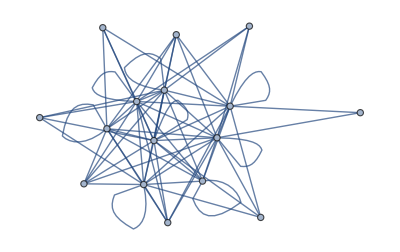

```mathematica
firstAlgebraGraph[firstAlgebra]=gaAlgebraMultiplicationTableGraph[firstAlgebra]
```

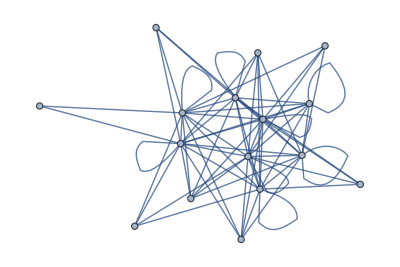

```mathematica
secondAlgebraGraph[secondAlgebra]=gaAlgebraMultiplicationTableGraph[secondAlgebra]
```

```mathematica
IsomorphicGraphQ[secondAlgebraGraph[secondAlgebra],firstAlgebraGraph[firstAlgebra]]
```

True

Now find isomorphisms between geometric algebras (with respect to geometric product, not commutator product)

We do not need all isomorphisms, just one is enough

```mathematica
allIsomorphisms[firstAlgebra->secondAlgebra]=FindGraphIsomorphism[firstAlgebraGraph[firstAlgebra],secondAlgebraGraph[secondAlgebra],All]
Table[isomorphismRules[firstAlgebra->secondAlgebra,n]=allIsomorphisms[firstAlgebra->secondAlgebra][[n]],{n,1,Length[allIsomorphisms[firstAlgebra->secondAlgebra]]}];isomorphismRules[firstAlgebra->secondAlgebra,1]
```

{<|-1→-1,12300→3120,13300→2120,23300→23120,123300→123120,1→1,1300→1120,2300→13120,3300→12120,-1300→-1120,-2300→-13120,-3300→-12120,-12300→-3120,-13300→-2120,-23300→-23120,-123300→-123120|>,<|-1→-1,12300→23120,13300→2120,23300→3120,123300→123120,1→1,1300→12120,2300→13120,3300→1120,-1300→-12120,-2300→-13120,-3300→-1120,-12300→-23120,-13300→-2120,-23300→-3120,-123300→-123120|>}

<|-1→-1,12300→3120,13300→2120,23300→23120,123300→123120,1→1,1300→1120,2300→13120,3300→12120,-1300→-1120,-2300→-13120,-3300→-12120,-12300→-3120,-13300→-2120,-23300→-23120,-123300→-123120|>

Make vector + bivector base, with respect to the algebras isomorphisms

```mathematica
allIsomorphisms[firstAlgebra->secondAlgebra]//Length
```